```mathematica
$HistoryLength=1;
```

```mathematica
a = Import["~/tmp/experiments/ComplexPExp2/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxm= Take[q, {1, Length[q], 100}];
lcomplexxm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/PseudoOptimalExp2/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxPm = Take[q, {1, Length[q], 100}];
lcomplexxPm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimpleJumpExp2/finalGrid.txt", "Table"];
q = Map[Mean, a];
complexxRm = Take[q, {1, Length[q], 100}];
lcomplexxRm = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimplePRExp2/finalGrid.txt", "Table"];
q = Map[Mean, a];
exclusiveem = Take[q, {1, Length[q], 100}];
lexclusiveem = Take[a, {1, Length[a], 100}];
```

```mathematica
a = Import["~/tmp/experiments/SimpleExp2/finalGrid.txt", "Table"];
q = Map[Mean, a];
optimallm = Take[q, {1, Length[q], 100}];
loptimallm  = Take[a, {1, Length[a], 100}];
```

```mathematica
rlcomplexxPm = lcomplexxPm[[2000]]
rlcomplexxRm = lcomplexxRm[[2000]]
rlcomplexxm = lcomplexxm[[2000]]
rlsimpleePm = lsimpleePm[[2000]]
rlsimpleeRm = lsimpleeRm[[2000]]
rlsimpleem = lsimpleem[[2000]]
rloptimallm = loptimallm[[2000]]
rlrandommm = lrandommm[[2000]]
rlrseannm = lseannm[[2000]]
rlexclusiveem = lexclusiveem[[2000]]
```

{7836.,6776.,7308.,7424.,6093.,8401.,6313.,6700.,6042.,7807.,7271.,6928.,7339.,7533.,6227.,6133.,6773.,6334.,8410.,6890.,5759.,6887.,6442.,6250.,7425.,6587.,6399.,5844.,5699.,6818.,6629.,6715.,6829.,7020.,7231.,6586.,7616.,5779.,6522.,7020.,7153.,6875.,7067.,7595.,6183.,6679.,5602.,6003.,6609.,7598.,6689.,6385.,6138.,5752.,5936.,6079.,7419.,6411.,7251.,5636.,7429.,6679.,7004.,6117.,5758.,7679.,6804.,6998.,6167.,5523.,6639.,7559.,7539.,6222.,6989.,6462.,6136.,6812.,6303.,7190.,6745.,7291.,7842.,7044.,6386.,6223.,6273.,5516.,6475.,7035.,5825.,6853.,5690.,6885.,6173.,7134.,6012.,7258.,8631.,6696.}

{6158.,8154.,7079.,5833.,5498.,7021.,7835.,5741.,7181.,6849.,6799.,6128.,7149.,6711.,4874.,8008.,5895.,8317.,5491.,6194.,7382.,6397.,7322.,6127.,7383.,7359.,7743.,8867.,6452.,7541.,6446.,6652.,6649.,6969.,7374.,7608.,7280.,6890.,6182.,7793.,7239.,6721.,8460.,6424.,5687.,7508.,5608.,7066.,6332.,6408.,8072.,6844.,6758.,7820.,5765.,6262.,6664.,5720.,6292.,7306.,6865.,5866.,6378.,6927.,6465.,6298.,7074.,6385.,5726.,6135.,8118.,6793.,8023.,6555.,7953.,5510.,5219.,6672.,6773.,7614.,6272.,8235.,6635.,6792.,7116.,7624.,6675.,6862.,6959.,6431.,7340.,6679.,6500.,7022.,7396.,7872.,6353.,6720.,7137.,7694.}

{5661.,5707.,5617.,7057.,6376.,6657.,7066.,6896.,6287.,5816.,6428.,6635.,6042.,6977.,6298.,5812.,5408.,6390.,6394.,6308.,5517.,5851.,5364.,6144.,6550.,7011.,7102.,5830.,6131.,6244.,6830.,7311.,6950.,6934.,6827.,6281.,6471.,6663.,7227.,6168.,6033.,6050.,6364.,6466.,5915.,6636.,6083.,6053.,6402.,6144.,7697.,5931.,6624.,6463.,6223.,5897.,6268.,6448.,6018.,6115.,6159.,6858.,6056.,7167.,5993.,6351.,7034.,6553.,6302.,6673.,7116.,7368.,6268.,6846.,6136.,7024.,6438.,6397.,6708.,6222.,6116.,7090.,7042.,5817.,5633.,5735.,6959.,7443.,6426.,6176.,5823.,6098.,6235.,6173.,6603.,5650.,6129.,8141.,6451.,7085.}

Part::partd: Part specification lsimpleePm ⟦ 2000 ⟧ is longer than depth of object.

lsimpleePm⟦2000⟧

Part::partd: Part specification lsimpleeRm ⟦ 2000 ⟧ is longer than depth of object.

lsimpleeRm⟦2000⟧

Part::partd: Part specification lsimpleem ⟦ 2000 ⟧ is longer than depth of object.

lsimpleem⟦2000⟧

{5724.,7209.,5699.,5704.,6207.,6843.,6475.,6644.,6421.,7151.,6266.,6685.,6232.,6277.,6885.,5655.,7106.,6178.,6167.,6765.,6225.,5904.,6145.,7053.,7055.,6091.,5760.,6929.,6746.,6150.,7080.,6766.,7144.,6072.,6848.,7130.,6204.,6257.,5699.,7011.,6121.,6947.,7213.,6469.,6101.,6678.,5399.,6450.,7595.,5562.,6017.,7490.,6828.,6206.,6478.,6842.,6611.,7021.,6504.,7320.,6700.,6494.,7360.,5760.,6607.,6031.,6745.,7587.,6475.,6257.,7203.,6975.,6488.,6469.,6041.,5597.,6846.,6564.,6607.,5997.,6832.,6272.,6309.,6246.,5752.,6479.,6569.,6001.,6614.,6353.,7636.,7310.,6544.,7135.,6455.,6568.,6378.,6252.,6263.,6755.}

Part::partd: Part specification lrandommm ⟦ 2000 ⟧ is longer than depth of object.

lrandommm⟦2000⟧

Part::partd: Part specification lseannm ⟦ 2000 ⟧ is longer than depth of object.

lseannm⟦2000⟧

{6439.,5568.,5890.,7121.,5425.,6033.,6184.,6141.,6156.,6728.,6396.,5612.,7350.,6017.,6587.,6618.,7412.,6082.,6287.,7755.,7094.,6373.,6072.,6122.,6497.,6438.,5936.,6771.,6415.,6838.,5557.,7651.,6926.,6340.,6089.,6220.,5755.,7519.,6369.,5888.,6288.,6972.,6055.,5922.,7192.,6071.,6952.,6459.,6708.,6651.,5850.,5338.,6695.,5540.,6848.,6707.,6202.,6100.,6916.,7025.,5420.,5377.,6388.,5871.,5414.,6451.,6063.,6440.,5289.,6426.,5562.,7057.,6000.,6634.,6629.,7219.,5347.,6125.,6521.,6010.,6239.,6796.,7054.,6593.,5569.,6243.,6574.,6852.,6095.,5953.,6083.,6711.,7274.,6886.,6244.,6634.,5754.,6619.,5611.,5973.}

```mathematica
alcomplexxPm = Map[Function[x, List[1,x]], rlcomplexxPm]
alcomplexxRm = Map[Function[x, List[2,x]], rlcomplexxRm]
alcomplexxm = Map[Function[x, List[3,x]], rlcomplexxm]
alsimpleePm = Map[Function[x, List[4,x]], rlsimpleePm]
alsimpleeRm = Map[Function[x, List[5,x]], rlsimpleeRm]
alsimpleem = Map[Function[x, List[6,x]], rlsimpleem]
aloptimallm = Map[Function[x, List[7,x]], rloptimallm]
alrandommm = Map[Function[x, List[8,x]], rlrandommm]

alseannm = Map[Function[x, List[9,x]], rlrseannm]
alexcluivem = Map[Function[x, List[10,x]], rlexclusiveem]
```

{{1,7836.},{1,6776.},{1,7308.},{1,7424.},{1,6093.},{1,8401.},{1,6313.},{1,6700.},{1,6042.},{1,7807.},{1,7271.},{1,6928.},{1,7339.},{1,7533.},{1,6227.},{1,6133.},{1,6773.},{1,6334.},{1,8410.},{1,6890.},{1,5759.},{1,6887.},{1,6442.},{1,6250.},{1,7425.},{1,6587.},{1,6399.},{1,5844.},{1,5699.},{1,6818.},{1,6629.},{1,6715.},{1,6829.},{1,7020.},{1,7231.},{1,6586.},{1,7616.},{1,5779.},{1,6522.},{1,7020.},{1,7153.},{1,6875.},{1,7067.},{1,7595.},{1,6183.},{1,6679.},{1,5602.},{1,6003.},{1,6609.},{1,7598.},{1,6689.},{1,6385.},{1,6138.},{1,5752.},{1,5936.},{1,6079.},{1,7419.},{1,6411.},{1,7251.},{1,5636.},{1,7429.},{1,6679.},{1,7004.},{1,6117.},{1,5758.},{1,7679.},{1,6804.},{1,6998.},{1,6167.},{1,5523.},{1,6639.},{1,7559.},{1,7539.},{1,6222.},{1,6989.},{1,6462.},{1,6136.},{1,6812.},{1,6303.},{1,7190.},{1,6745.},{1,7291.},{1,7842.},{1,7044.},{1,6386.},{1,6223.},{1,6273.},{1,5516.},{1,6475.},{1,7035.},{1,5825.},{1,6853.},{1,5690.},{1,6885.},{1,6173.},{1,7134.},{1,6012.},{1,7258.},{1,8631.},{1,6696.}}

{{2,6158.},{2,8154.},{2,7079.},{2,5833.},{2,5498.},{2,7021.},{2,7835.},{2,5741.},{2,7181.},{2,6849.},{2,6799.},{2,6128.},{2,7149.},{2,6711.},{2,4874.},{2,8008.},{2,5895.},{2,8317.},{2,5491.},{2,6194.},{2,7382.},{2,6397.},{2,7322.},{2,6127.},{2,7383.},{2,7359.},{2,7743.},{2,8867.},{2,6452.},{2,7541.},{2,6446.},{2,6652.},{2,6649.},{2,6969.},{2,7374.},{2,7608.},{2,7280.},{2,6890.},{2,6182.},{2,7793.},{2,7239.},{2,6721.},{2,8460.},{2,6424.},{2,5687.},{2,7508.},{2,5608.},{2,7066.},{2,6332.},{2,6408.},{2,8072.},{2,6844.},{2,6758.},{2,7820.},{2,5765.},{2,6262.},{2,6664.},{2,5720.},{2,6292.},{2,7306.},{2,6865.},{2,5866.},{2,6378.},{2,6927.},{2,6465.},{2,6298.},{2,7074.},{2,6385.},{2,5726.},{2,6135.},{2,8118.},{2,6793.},{2,8023.},{2,6555.},{2,7953.},{2,5510.},{2,5219.},{2,6672.},{2,6773.},{2,7614.},{2,6272.},{2,8235.},{2,6635.},{2,6792.},{2,7116.},{2,7624.},{2,6675.},{2,6862.},{2,6959.},{2,6431.},{2,7340.},{2,6679.},{2,6500.},{2,7022.},{2,7396.},{2,7872.},{2,6353.},{2,6720.},{2,7137.},{2,7694.}}

{{3,5661.},{3,5707.},{3,5617.},{3,7057.},{3,6376.},{3,6657.},{3,7066.},{3,6896.},{3,6287.},{3,5816.},{3,6428.},{3,6635.},{3,6042.},{3,6977.},{3,6298.},{3,5812.},{3,5408.},{3,6390.},{3,6394.},{3,6308.},{3,5517.},{3,5851.},{3,5364.},{3,6144.},{3,6550.},{3,7011.},{3,7102.},{3,5830.},{3,6131.},{3,6244.},{3,6830.},{3,7311.},{3,6950.},{3,6934.},{3,6827.},{3,6281.},{3,6471.},{3,6663.},{3,7227.},{3,6168.},{3,6033.},{3,6050.},{3,6364.},{3,6466.},{3,5915.},{3,6636.},{3,6083.},{3,6053.},{3,6402.},{3,6144.},{3,7697.},{3,5931.},{3,6624.},{3,6463.},{3,6223.},{3,5897.},{3,6268.},{3,6448.},{3,6018.},{3,6115.},{3,6159.},{3,6858.},{3,6056.},{3,7167.},{3,5993.},{3,6351.},{3,7034.},{3,6553.},{3,6302.},{3,6673.},{3,7116.},{3,7368.},{3,6268.},{3,6846.},{3,6136.},{3,7024.},{3,6438.},{3,6397.},{3,6708.},{3,6222.},{3,6116.},{3,7090.},{3,7042.},{3,5817.},{3,5633.},{3,5735.},{3,6959.},{3,7443.},{3,6426.},{3,6176.},{3,5823.},{3,6098.},{3,6235.},{3,6173.},{3,6603.},{3,5650.},{3,6129.},{3,8141.},{3,6451.},{3,7085.}}

Part::partw: Part {4, 2000} of {4, lsimpleePm} does not exist.

{4,lsimpleePm}⟦{4,2000}⟧

Part::partw: Part {5, 2000} of {5, lsimpleeRm} does not exist.

{5,lsimpleeRm}⟦{5,2000}⟧

Part::partw: Part {6, 2000} of {6, lsimpleem} does not exist.

{6,lsimpleem}⟦{6,2000}⟧

{{7,5724.},{7,7209.},{7,5699.},{7,5704.},{7,6207.},{7,6843.},{7,6475.},{7,6644.},{7,6421.},{7,7151.},{7,6266.},{7,6685.},{7,6232.},{7,6277.},{7,6885.},{7,5655.},{7,7106.},{7,6178.},{7,6167.},{7,6765.},{7,6225.},{7,5904.},{7,6145.},{7,7053.},{7,7055.},{7,6091.},{7,5760.},{7,6929.},{7,6746.},{7,6150.},{7,7080.},{7,6766.},{7,7144.},{7,6072.},{7,6848.},{7,7130.},{7,6204.},{7,6257.},{7,5699.},{7,7011.},{7,6121.},{7,6947.},{7,7213.},{7,6469.},{7,6101.},{7,6678.},{7,5399.},{7,6450.},{7,7595.},{7,5562.},{7,6017.},{7,7490.},{7,6828.},{7,6206.},{7,6478.},{7,6842.},{7,6611.},{7,7021.},{7,6504.},{7,7320.},{7,6700.},{7,6494.},{7,7360.},{7,5760.},{7,6607.},{7,6031.},{7,6745.},{7,7587.},{7,6475.},{7,6257.},{7,7203.},{7,6975.},{7,6488.},{7,6469.},{7,6041.},{7,5597.},{7,6846.},{7,6564.},{7,6607.},{7,5997.},{7,6832.},{7,6272.},{7,6309.},{7,6246.},{7,5752.},{7,6479.},{7,6569.},{7,6001.},{7,6614.},{7,6353.},{7,7636.},{7,7310.},{7,6544.},{7,7135.},{7,6455.},{7,6568.},{7,6378.},{7,6252.},{7,6263.},{7,6755.}}

Part::partw: Part {8, 2000} of {8, lrandommm} does not exist.

{8,lrandommm}⟦{8,2000}⟧

Part::partw: Part {9, 2000} of {9, lseannm} does not exist.

{9,lseannm}⟦{9,2000}⟧

{{10,6439.},{10,5568.},{10,5890.},{10,7121.},{10,5425.},{10,6033.},{10,6184.},{10,6141.},{10,6156.},{10,6728.},{10,6396.},{10,5612.},{10,7350.},{10,6017.},{10,6587.},{10,6618.},{10,7412.},{10,6082.},{10,6287.},{10,7755.},{10,7094.},{10,6373.},{10,6072.},{10,6122.},{10,6497.},{10,6438.},{10,5936.},{10,6771.},{10,6415.},{10,6838.},{10,5557.},{10,7651.},{10,6926.},{10,6340.},{10,6089.},{10,6220.},{10,5755.},{10,7519.},{10,6369.},{10,5888.},{10,6288.},{10,6972.},{10,6055.},{10,5922.},{10,7192.},{10,6071.},{10,6952.},{10,6459.},{10,6708.},{10,6651.},{10,5850.},{10,5338.},{10,6695.},{10,5540.},{10,6848.},{10,6707.},{10,6202.},{10,6100.},{10,6916.},{10,7025.},{10,5420.},{10,5377.},{10,6388.},{10,5871.},{10,5414.},{10,6451.},{10,6063.},{10,6440.},{10,5289.},{10,6426.},{10,5562.},{10,7057.},{10,6000.},{10,6634.},{10,6629.},{10,7219.},{10,5347.},{10,6125.},{10,6521.},{10,6010.},{10,6239.},{10,6796.},{10,7054.},{10,6593.},{10,5569.},{10,6243.},{10,6574.},{10,6852.},{10,6095.},{10,5953.},{10,6083.},{10,6711.},{10,7274.},{10,6886.},{10,6244.},{10,6634.},{10,5754.},{10,6619.},{10,5611.},{10,5973.}}

```mathematica
Needs["ANOVA`"]

ANOVA[Join[alcomplexxRm,alcomplexxPm,alcomplexxm,aloptimallm,alexcluivem], PostTests->Tukey]
```

{ANOVA→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 4 | 1.68168×10^7 | 4.2042×10^6 | 11.1177 | 1.21114×10^-8
Error | 495 | 1.87186×10^8 | 378154. |  | 
Total | 499 | 2.04003×10^8 |  |  | ,CellMeans→All | 6568.53
Model[1] | 6716.51
Model[2] | 6839.5
Model[3] | 6415.62
Model[7] | 6519.4
Model[10] | 6351.62,PostTests→{Model→Tukey | {{1,3},{2,3},{2,7},{1,10},{2,10}}}}

```mathematica
grandommm =  ListPlot[Take[randommm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[randommm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[randommm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0.3`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.2`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[randommm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

```mathematica
gseannm =  ListPlot[Take[seannm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[seannm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[seannm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0.3`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.2`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[seannm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

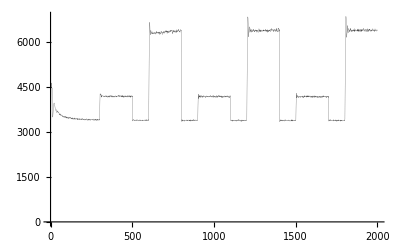

-Graphics-

```mathematica
goptimallm =  ListPlot[Take[optimallm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GrayLevel[0.3], Thickness[0.0005]}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2029.8, 3833.77, 5256.5, 6257.29, 6889.43, 7150.54, 7243.69, 7107.68, 7008.33, 6966.05, 6832.87, 6839.4, 6529.36, 6240.51, 5986.95, 5639.03, « 19 », 4456.45, 4489.65, 4502.28, 4496.67, 4423.88, 4484.37, 4436.23, 4398.73, 4369.48, 4350.76, 4293.52, 4253.29, 4165.99, 4127.44, 4147.43, « 1950 »}, « 2 », « 9 » → « 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2029.8,3833.77,5256.5,6257.29,6889.43,7150.54,7243.69,7107.68,7008.33,6966.05,6832.87,6839.4,6529.36,6240.51,5986.95,5639.03,5185.6,4796.66,4584.96,4485.63,4352.84,4356.16,4357.08,4334.77,4357.31,4322.02,4274.97,4311.28,4361.75,4391.29,4425.6,4401.14,4442.51,4476.72,4437.13,4456.45,4489.65,4502.28,4496.67,4423.88,4484.37,4436.23,4398.73,4369.48,4350.76,4293.52,4253.29,4165.99,4127.44,4147.43,4078.11,4121.12,4090.32,4042.47,4028.48,3977.87,3961.5,3925.5,3939.87,3899.86,3866.98,3868.27,3810.04,3810.11,3797.07,3814.44,3721.68,3813.65,3760.34,3721.48,3737.01,3691.5,3676.82,3659.44,3678.36,3670.05,3672.37,3675.96,3673.56,3635.82,3620.4,3630.81,3602.74,3633.94,3575.49,3627.98,3604.51,3608.9,3623.57,3593.41,3575.67,3585.64,3574.13,3592.02,3625.78,3615.97,3564.75,3555.61,3564.05,3528.69,3555.54,3564.22,3539.73,3535.7,3588.56,3544.49,3567.87,3544.44,3536.6,3505.04,3514.2,3543.76,3540.09,3520.69,3529.72,3541.6,3522.02,3545.44,3542.23,3484.04,3507.77,3514.81,3512.48,3500.61,3526.39,3512.21,3459.61,3484.61,3535.21,3502.94,3520.93,3514.,3509.8,3502.1,3530.64,3514.3,3496.32,3524.17,3504.58,3522.81,3522.65,3504.49,3502.4,3513.97,3482.99,3493.92,3529.89,3517.17,3526.1,3499.07,3499.83,3505.96,3466.67,3534.1,3495.17,3503.3,3528.19,3479.3,3493.08,3499.42,3494.99,3477.81,3490.38,3481.79,3483.14,3524.15,3504.12,3504.2,3505.18,3514.74,3511.24,3517.25,3489.01,3484.98,3528.78,3494.79,3476.23,3471.01,3500.34,3497.66,3515.67,3483.94,3477.63,3488.3,3457.69,3484.7,3471.69,3452.13,3492.9,3510.37,3519.81,3520.86,3477.09,3498.76,3497.56,3519.58,3481.94,3496.01,3471.3,3485.91,3513.16,3547.65,3538.24,3492.04,3460.98,3481.22,3490.54,3496.1,3497.75,3487.34,3483.31,3494.05,3515.53,3494.23,3473.8,3517.84,3506.5,3474.96,3505.7,3494.58,3488.82,3506.69,3499.95,3474.95,3479.09,3467.44,3534.66,3487.25,3500.65,3471.82,3500.34,3514.48,3508.2,3473.98,3493.04,3520.24,3513.48,3474.45,3475.79,3520.07,3492.4,3472.91,3449.13,3458.36,3497.69,3441.42,3475.89,3500.53,3475.38,3516.14,3508.65,3488.42,3481.21,3520.51,3481.61,3465.4,3487.27,3496.59,3487.72,3482.39,3490.71,3476.07,3495.21,3501.02,3456.77,3465.2,3471.36,3455.58,3493.74,3452.54,3499.58,3477.46,3502.19,3464.86,3507.65,3482.23,3472.56,3464.29,3516.71,3466.65,3476.1,3482.25,3481.36,3492.66,3470.43,3505.43,3492.8,3472.87,3480.78,3465.33,3462.27,3451.92,3478.08,3455.31,3468.04,3467.5,3436.93,3508.69,3498.62,3461.64,3516.14,4049.77,4642.68,4919.09,4881.67,4756.92,4579.09,4486.76,4484.75,4419.83,4484.75,4459.36,4415.73,4429.74,4370.14,4372.95,4374.98,4389.46,4360.34,4352.18,4330.15,4380.16,4365.66,4379.59,4372.98,4337.71,4313.44,4330.07,4363.3,4344.16,4339.62,4345.09,4312.74,4294.65,4317.46,4328.71,4339.63,4295.56,4322.68,4292.39,4343.13,4341.2,4314.82,4335.52,4343.86,4304.55,4284.17,4293.74,4311.76,4287.57,4325.17,4319.28,4244.44,4248.48,4335.06,4345.62,4328.47,4292.68,4367.35,4349.02,4243.95,4333.38,4335.09,4316.65,4331.2,4340.94,4293.1,4297.76,4344.87,4328.43,4369.89,4322.81,4320.25,4331.56,4333.07,4316.12,4322.5,4316.38,4311.7,4365.56,4367.22,4359.7,4333.18,4307.23,4311.11,4356.52,4358.55,4354.78,4316.24,4333.11,4314.32,4330.23,4312.12,4328.94,4351.76,4332.71,4321.55,4332.61,4347.57,4313.09,4290.61,4317.58,4314.64,4323.04,4359.51,4326.11,4327.29,4354.22,4333.7,4299.54,4328.19,4370.11,4338.09,4334.47,4317.08,4365.17,4356.17,4319.32,4368.5,4330.8,4338.5,4346.28,4338.88,4376.15,4332.84,4289.34,4334.45,4312.92,4269.46,4317.37,4327.89,4358.76,4351.76,4318.56,4281.51,4301.03,4274.34,4367.33,4297.11,4353.81,4321.98,4312.13,4279.36,4339.93,4313.01,4325.19,4318.87,4326.08,4330.78,4309.5,4312.33,4335.43,4318.04,4288.43,4325.19,4292.76,4309.38,4281.49,4306.61,4312.41,4328.16,4316.9,4296.54,4304.17,4334.18,4286.85,4302.18,4309.67,4299.68,4324.85,4340.4,4294.85,4321.82,4321.22,4338.68,4342.98,4279.45,4340.52,4339.75,4364.11,4361.97,4293.95,4324.01,4363.34,4307.92,4337.32,4316.05,4324.89,4362.17,4304.52,4348.75,4315.93,4340.47,4322.27,4328.22,4306.33,4316.66,4318.05,4322.62,4322.55,4285.78,3644.41,3551.84,3523.5,3498.2,3491.13,3516.77,3486.17,3503.34,3456.17,3509.19,3521.69,3495.03,3478.34,3496.53,3476.42,3463.72,3496.34,3522.26,3486.22,3502.37,3500.58,3495.77,3463.28,3500.12,3503.1,3446.78,3481.13,3518.,3470.86,3465.36,3472.98,3473.72,3489.87,3468.78,3505.64,3477.82,3461.26,3450.43,3456.71,3479.5,3455.04,3453.68,3506.97,3482.22,3469.08,3467.58,3476.36,3460.39,3447.77,3440.93,3440.82,3457.08,3478.53,3485.51,3481.32,3486.81,3499.79,3515.34,3463.87,3478.44,3497.01,3460.09,3461.22,3455.85,3459.24,3465.43,3469.17,3454.39,3453.33,3502.24,3474.9,3457.37,3475.11,3444.93,3443.79,3453.28,3486.39,3452.74,3468.96,3470.73,3474.68,3471.59,3464.79,3456.17,3483.95,3505.26,3485.1,3477.32,3463.53,3485.94,3478.,3472.54,3468.63,3465.61,3467.07,3455.29,3483.69,3482.22,3462.15,3514.48,4507.75,5571.32,6457.17,7090.56,7449.35,7720.03,7741.84,7566.01,7431.66,7130.72,6977.06,6852.05,6714.82,6749.24,6700.1,6730.33,6705.41,6707.06,6608.81,6588.06,6590.08,6627.14,6595.92,6589.34,6601.85,6531.19,6568.12,6576.56,6494.29,6530.2,6579.33,6597.85,6481.51,6461.24,6492.62,6581.16,6523.71,6481.39,6502.56,6488.77,6436.6,6518.6,6536.45,6558.25,6471.11,6528.19,6497.44,6478.18,6484.57,6515.7,6484.51,6496.5,6397.68,6451.91,6452.88,6582.04,6550.57,6569.77,6564.12,6520.99,6505.81,6499.16,6520.85,6489.54,6520.53,6440.2,6490.47,6484.88,6486.71,6541.76,6452.89,6496.49,6447.96,6459.41,6487.58,6555.51,6558.97,6548.3,6554.89,6559.6,6581.,6508.15,6582.7,6494.35,6511.54,6458.97,6491.65,6569.77,6529.34,6519.13,6501.12,6495.7,6478.69,6515.33,6550.31,6492.19,6510.86,6536.38,6474.66,6472.3,6503.94,6490.77,6525.17,6507.72,6563.91,6533.35,6447.03,6490.14,6453.32,6485.23,6496.47,6503.86,6526.99,6534.,6546.68,6513.82,6448.44,6493.95,6496.09,6497.09,6521.84,6510.22,6468.15,6496.46,6473.92,6502.69,6507.66,6614.29,6590.25,6509.02,6547.48,6464.21,6462.17,6490.12,6486.29,6529.99,6486.4,6476.74,6486.39,6495.92,6551.61,6495.14,6533.26,6504.04,6478.74,6488.67,6530.64,6497.42,6475.47,6545.,6535.91,6555.4,6578.69,6524.28,6527.59,6552.44,6529.22,6488.8,6494.94,6505.05,6516.68,6491.83,6530.24,6540.83,6473.69,6535.7,6528.75,6457.64,6423.17,6446.38,6517.54,6504.45,6550.54,6533.73,6497.19,6506.21,6421.94,6540.16,6496.76,6590.5,6538.53,6538.17,6589.71,6544.1,6565.99,6522.91,6509.71,6507.51,6553.56,6505.16,6509.7,6557.62,6531.78,6507.16,6484.28,6475.31,6489.32,6524.84,6449.43,6419.75,4106.69,3542.32,3484.2,3509.13,3494.83,3485.92,3502.98,3491.9,3484.38,3497.9,3480.95,3466.19,3460.79,3513.23,3508.1,3468.05,3477.75,3505.59,3506.02,3447.5,3486.01,3457.37,3465.9,3471.84,3485.22,3476.79,3497.98,3473.27,3461.99,3479.85,3502.57,3479.32,3457.75,3472.84,3453.67,3487.57,3488.27,3445.39,3460.37,3454.8,3460.79,3466.48,3430.88,3488.09,3469.26,3494.14,3468.77,3475.68,3462.13,3487.97,3437.09,3486.03,3517.45,3450.33,3458.73,3430.87,3474.33,3448.,3464.91,3455.56,3471.07,3463.12,3471.85,3449.49,3472.85,3470.4,3458.93,3446.71,3459.01,3464.22,3459.44,3452.92,3452.85,3473.18,3455.84,3484.78,3480.84,3463.99,3476.06,3459.66,3460.79,3473.84,3493.97,3470.3,3450.43,3439.67,3436.2,3482.27,3436.29,3478.91,3434.76,3475.97,3458.02,3454.98,3494.58,3447.6,3460.05,3429.33,3470.33,3497.7,3920.64,4353.98,4616.11,4619.23,4451.23,4398.01,4367.67,4401.77,4429.59,4398.91,4377.93,4374.28,4382.73,4377.87,4361.84,4382.74,4382.27,4372.49,4360.44,4345.67,4337.3,4382.77,4391.66,4372.34,4302.27,4349.52,4355.4,4357.95,4351.66,4311.28,4343.4,4331.47,4351.14,4349.98,4372.15,4354.16,4315.75,4340.16,4335.36,4331.35,4307.2,4312.94,4318.5,4339.7,4290.55,4333.08,4326.86,4328.19,4319.18,4317.61,4350.08,4301.45,4322.27,4285.05,4275.08,4307.27,4327.01,4304.54,4280.55,4338.35,4312.31,4296.36,4296.18,4356.79,4337.68,4313.48,4311.71,4297.82,4317.29,4299.4,4298.52,4336.61,4310.26,4283.44,4309.29,4303.65,4310.11,4309.41,4261.81,4312.5,4295.95,4295.93,4317.96,4275.66,4301.91,4325.78,4321.3,4326.41,4273.38,4303.89,4298.96,4316.68,4304.48,4309.59,4282.49,4275.05,4284.87,4342.49,4333.48,4328.64,4311.49,4307.51,4310.01,4290.46,4346.51,4301.93,4318.77,4331.67,4332.89,4300.39,4320.9,4284.64,4285.83,4261.75,4280.75,4314.16,4316.59,4335.64,4293.6,4279.92,4313.39,4306.79,4326.7,4317.97,4323.62,4276.71,4271.,4338.45,4302.14,4338.46,4292.15,4279.12,4336.97,4341.77,4346.44,4317.97,4299.09,4287.02,4331.42,4353.22,4301.02,4291.42,4313.89,4292.66,4285.95,4315.76,4297.61,4313.71,4320.12,4305.4,4296.09,4299.14,4297.59,4324.01,4311.89,4286.23,4325.59,4329.15,4326.42,4303.,4277.33,4321.12,4332.62,4330.73,4319.82,4311.41,4291.14,4348.01,4300.94,4316.68,4285.58,4300.13,4294.81,4334.75,4300.66,4288.22,4290.54,4318.3,4295.93,4256.66,4271.1,4293.01,4307.02,4341.58,4305.61,4315.56,4290.76,4262.36,4284.34,4351.8,4307.83,4281.89,4321.82,4310.31,4335.43,4324.47,4268.98,4299.04,4308.43,4281.45,3620.5,3532.03,3490.2,3496.98,3481.85,3475.69,3471.98,3459.07,3474.62,3478.95,3452.13,3507.97,3475.57,3440.23,3452.4,3501.17,3445.64,3479.75,3458.44,3461.55,3480.31,3460.87,3455.34,3504.37,3475.03,3477.08,3471.32,3478.14,3464.29,3477.37,3461.92,3475.74,3449.69,3424.08,3444.08,3474.32,3479.46,3475.03,3459.38,3480.58,3440.8,3471.6,3464.87,3466.69,3465.02,3482.61,3449.1,3479.8,3477.03,3456.03,3470.13,3472.18,3438.36,3482.88,3477.02,3448.28,3446.39,3481.29,3468.75,3458.36,3452.65,3484.87,3456.89,3447.01,3457.9,3443.96,3466.23,3468.39,3444.04,3441.28,3439.75,3476.66,3448.52,3471.89,3467.87,3445.3,3451.09,3474.02,3471.48,3470.57,3469.71,3474.06,3457.62,3425.47,3463.8,3462.92,3435.44,3460.66,3457.72,3413.18,3442.03,3463.56,3432.72,3456.56,3443.55,3448.24,3466.4,3448.01,3495.2,3526.66,4480.02,5430.39,6216.75,6836.93,7197.15,7481.94,7469.34,7373.86,7103.76,6857.82,6689.12,6690.88,6694.82,6699.39,6707.56,6816.19,6836.41,6718.06,6781.11,6688.61,6642.69,6581.57,6600.2,6654.69,6617.92,6693.2,6693.37,6641.78,6570.46,6617.16,6558.69,6619.72,6685.41,6652.3,6630.72,6603.84,6524.11,6558.02,6553.3,6549.69,6517.44,6597.34,6631.39,6608.93,6605.11,6601.44,6577.96,6619.76,6562.19,6526.28,6534.63,6556.43,6542.57,6535.64,6567.46,6517.75,6560.73,6653.59,6617.59,6643.73,6636.82,6629.3,6575.37,6575.24,6515.97,6533.32,6532.19,6528.06,6588.22,6564.97,6618.99,6507.82,6596.4,6583.65,6538.47,6546.47,6551.96,6551.71,6563.19,6488.62,6565.65,6523.54,6506.78,6520.6,6509.51,6544.15,6556.35,6563.13,6586.42,6489.21,6541.91,6542.26,6502.25,6552.86,6632.62,6556.9,6538.94,6588.82,6515.44,6523.64,6529.91,6561.69,6583.62,6597.68,6529.85,6554.23,6439.51,6458.42,6549.32,6531.3,6514.85,6590.36,6615.82,6586.6,6487.47,6487.96,6528.61,6518.58,6541.94,6556.87,6501.27,6505.97,6514.11,6519.58,6557.86,6573.44,6586.04,6541.11,6514.74,6516.46,6548.05,6585.17,6597.73,6528.96,6559.92,6501.48,6489.1,6558.95,6615.71,6518.89,6574.17,6460.11,6502.87,6494.53,6562.54,6616.11,6597.7,6556.44,6478.28,6442.57,6479.05,6509.45,6520.56,6546.38,6563.43,6522.13,6546.83,6521.91,6586.69,6553.29,6495.23,6467.45,6577.6,6586.78,6564.67,6502.15,6524.99,6477.24,6521.53,6488.18,6550.72,6542.63,6562.12,6560.58,6586.87,6548.27,6543.09,6571.38,6510.99,6503.78,6467.22,6507.75,6559.62,6536.12,6546.28,6525.01,6496.06,6557.23,6514.89,6521.9,6589.87,6593.97,6531.6,6526.66,6554.39,6513.04,6558.82,6561.33,6518.84,6518.32,4100.46,3506.05,3502.44,3491.97,3462.54,3490.1,3460.79,3469.47,3481.25,3477.81,3451.85,3483.91,3473.34,3445.03,3475.54,3459.68,3499.26,3464.94,3460.18,3485.67,3500.33,3456.56,3463.49,3506.7,3473.35,3482.29,3444.54,3497.12,3489.32,3458.74,3488.22,3437.29,3462.37,3492.38,3442.38,3496.27,3466.75,3470.66,3459.79,3448.27,3475.58,3467.52,3471.52,3484.25,3448.65,3481.28,3468.79,3497.52,3464.42,3460.5,3453.06,3436.76,3489.14,3459.18,3457.84,3452.75,3470.63,3456.67,3459.05,3482.43,3490.73,3480.04,3479.93,3487.31,3455.56,3458.46,3453.34,3494.96,3449.87,3461.32,3429.6,3464.82,3463.33,3477.07,3464.72,3473.73,3469.59,3442.47,3449.38,3502.42,3453.69,3486.35,3457.57,3468.29,3439.8,3495.52,3462.63,3447.41,3453.32,3499.92,3464.5,3450.84,3447.67,3487.68,3473.57,3467.55,3462.93,3445.42,3436.07,3519.86,3944.15,4314.47,4503.33,4525.64,4446.02,4333.85,4315.54,4372.11,4431.22,4413.53,4347.58,4328.87,4318.97,4358.62,4386.79,4370.75,4357.58,4323.4,4337.06,4362.05,4339.31,4359.91,4299.99,4334.66,4298.42,4329.33,4340.03,4312.06,4323.2,4327.74,4331.42,4340.74,4328.47,4274.41,4309.4,4302.17,4304.8,4341.23,4341.68,4277.34,4272.14,4308.08,4339.09,4337.93,4348.88,4316.18,4289.27,4309.61,4305.39,4284.12,4302.86,4290.81,4311.92,4325.01,4295.57,4321.01,4359.07,4329.36,4295.46,4286.58,4315.83,4286.39,4326.39,4346.74,4324.39,4304.66,4319.33,4295.83,4294.28,4285.4,4301.24,4272.57,4289.04,4250.17,4291.13,4320.12,4346.94,4293.02,4319.06,4304.41,4299.,4256.34,4266.96,4275.53,4249.03,4318.12,4319.18,4308.82,4309.,4283.25,4281.49,4290.24,4269.15,4312.51,4280.12,4303.29,4288.29,4257.83,4319.55,4294.75,4259.06,4275.61,4310.26,4310.91,4310.27,4339.6,4300.86,4280.27,4275.91,4277.51,4275.31,4297.08,4295.,4295.87,4284.39,4287.19,4342.22,4293.25,4302.56,4280.68,4272.17,4301.39,4272.48,4309.31,4267.55,4275.43,4308.32,4274.79,4327.61,4276.45,4277.03,4269.45,4321.71,4277.72,4330.09,4299.69,4291.33,4302.89,4279.75,4247.5,4303.43,4287.66,4309.22,4312.58,4270.28,4304.5,4283.75,4298.97,4306.95,4288.56,4316.15,4323.29,4314.51,4333.21,4294.33,4278.92,4272.06,4339.93,4330.4,4273.01,4286.2,4311.7,4317.98,4345.87,4285.31,4281.21,4274.19,4282.53,4303.52,4309.93,4316.46,4324.1,4292.3,4291.58,4299.44,4275.28,4332.64,4283.81,4276.88,4274.33,4279.21,4299.53,4276.07,4308.09,4279.02,4308.34,4278.15,4305.69,4244.86,4308.89,4303.99,4228.32,4287.74,4322.98,4342.32,4320.7,4323.74,4262.26,4291.78,4265.69,3670.85,3519.13,3488.96,3475.48,3491.85,3481.34,3475.43,3479.24,3464.97,3469.18,3477.62,3480.3,3485.56,3463.51,3465.89,3462.18,3473.18,3518.36,3477.05,3444.51,3478.56,3488.18,3481.34,3464.24,3450.86,3464.38,3485.76,3488.41,3494.11,3455.19,3491.99,3489.58,3467.31,3483.96,3470.13,3466.32,3460.71,3476.,3449.29,3488.01,3478.55,3500.83,3450.93,3479.13,3446.54,3478.48,3491.1,3512.87,3474.38,3444.02,3495.21,3490.54,3471.62,3462.16,3464.46,3467.93,3489.91,3478.48,3474.81,3458.87,3449.39,3472.9,3468.6,3441.87,3485.21,3466.83,3456.5,3486.4,3484.1,3475.45,3474.97,3445.39,3484.2,3458.28,3453.46,3466.69,3444.26,3500.1,3462.81,3494.37,3483.09,3495.77,3453.51,3472.89,3453.95,3467.9,3436.8,3494.25,3452.4,3432.86,3475.1,3488.11,3468.42,3488.01,3439.25,3482.57,3503.13,3472.1,3459.13,3501.11,4441.69,5385.59,6147.,6773.24,7181.33,7351.65,7326.68,7191.59,6925.19,6735.61,6540.31,6462.,6578.81,6678.96,6739.19,6782.69,6749.31,6729.72,6657.76,6618.96,6598.47,6675.13,6583.2,6543.26,6532.6,6554.68,6651.52,6668.74,6594.53,6630.93,6597.37,6582.97,6539.14,6557.61,6589.34,6610.89,6610.61,6633.58,6562.8,6544.68,6567.26,6610.29,6632.72,6646.89,6580.64,6566.9,6545.79,6504.4,6510.24,6557.36,6567.58,6614.48,6554.74,6509.8,6521.45,6458.33,6520.96,6587.88,6540.9,6603.82,6551.95,6565.38,6561.67,6519.24,6548.26,6541.12,6554.21,6567.17,6572.65,6527.08,6536.69,6524.1,6515.46,6530.26,6598.1,6529.34,6487.74,6524.75,6562.44,6519.9,6548.48,6521.12,6495.35,6565.35,6538.9,6591.23,6550.88,6510.17,6558.14,6546.19,6570.8,6536.21,6579.39,6576.36,6506.45,6564.63,6539.15,6488.36,6443.92,6495.88,6550.88,6548.43,6597.85,6535.87,6489.9,6472.32,6469.51,6465.67,6516.2,6528.36,6597.59,6522.81,6597.53,6604.64,6570.98,6572.17,6565.23,6546.42,6502.83,6537.03,6594.16,6578.04,6579.27,6588.81,6555.59,6528.5,6492.41,6508.32,6527.05,6494.31,6552.76,6473.29,6460.45,6497.5,6504.54,6520.43,6523.98,6537.71,6533.41,6510.17,6578.02,6547.72,6505.34,6492.28,6473.36,6506.88,6493.5,6513.1,6579.95,6560.68,6544.89,6520.66,6484.75,6509.12,6471.68,6419.49,6504.37,6480.59,6496.41,6541.75,6480.47,6529.46,6495.08,6537.58,6482.02,6549.29,6561.,6563.08,6574.31,6538.33,6535.54,6592.28,6567.42,6561.82,6483.45,6532.58,6487.68,6523.92,6510.29,6506.56,6536.43,6584.34,6534.91,6500.62,6456.38,6572.72,6570.13,6598.83,6523.32,6547.04,6555.83,6496.27,6565.46,6515.61,6482.84,6517.37,6505.67,6489.81,6519.4},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}]

```mathematica
gcomplexxPm = ListPlot[Take[complexxPm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Red, Thickness[0.001]}]
```

ListPlot::optx: Unknown option PlotJoined → True in {2029.15`, 3238.37`, 3692.7200000000003`, 3694.64`, 3605.71`, 3558.54`, 3587.06`, 3589.7400000000002`, 3583.23`, 3605.28`, 3616.03`, 3607.4300000000003`, 3623.33`, 3606.35`, 3636.58`, 3615.82`, 3582.6800000000003`, « 17 », 3609.2200000000003`, 3590.27`, 3592.55`, 3587.8`, 3591.51`, 3617.83`, 3637.08`, 3606.82`, 3623.52`, 3610.`, 3613.17`, 3591.89`, 3582.58`, 3601.78`, 3593.63`, 3632.84`, « 1950 »}, « 2 », PlotStyle → {InterpretationBox[ButtonBox[« 1 », Rule[Appearance, None], Rule[BaseStyle, List[]], Rule[BaselinePosition, Baseline], Rule[DefaultBaseStyle, List[]], RuleDelayed[ButtonFunction, With[List[Set[Typeset`box$, EvaluationBox[]]], If[Not[AbsoluteCurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2029.15,3238.37,3692.72,3694.64,3605.71,3558.54,3587.06,3589.74,3583.23,3605.28,3616.03,3607.43,3623.33,3606.35,3636.58,3615.82,3582.68,3619.22,3623.9,3585.39,3609.56,3613.19,3640.01,3621.15,3619.52,3575.97,3576.12,3625.71,3617.18,3593.09,3642.99,3605.16,3617.26,3628.99,3609.22,3590.27,3592.55,3587.8,3591.51,3617.83,3637.08,3606.82,3623.52,3610.,3613.17,3591.89,3582.58,3601.78,3593.63,3632.84,3575.81,3625.73,3609.14,3593.47,3561.74,3591.9,3578.84,3591.19,3632.33,3604.24,3622.74,3626.58,3560.67,3584.99,3565.21,3598.27,3620.39,3638.33,3625.67,3567.94,3617.35,3599.9,3605.22,3633.59,3615.,3644.36,3614.48,3583.74,3593.61,3631.14,3595.86,3628.49,3609.03,3605.48,3597.24,3601.35,3606.79,3622.71,3609.05,3593.9,3581.97,3576.32,3607.7,3614.38,3620.68,3603.19,3602.83,3607.36,3607.99,3605.55,3597.72,3598.65,3590.08,3600.38,3604.03,3579.84,3568.55,3610.91,3621.61,3639.06,3574.81,3586.39,3609.28,3616.87,3607.96,3614.07,3603.11,3613.45,3571.09,3616.85,3618.9,3576.53,3591.16,3617.93,3585.86,3587.24,3603.44,3597.89,3611.23,3623.89,3614.39,3615.02,3598.15,3600.61,3627.31,3624.85,3593.01,3607.92,3589.56,3634.78,3609.1,3595.68,3602.15,3605.18,3626.15,3609.87,3615.92,3638.04,3642.86,3636.96,3593.88,3603.67,3599.41,3589.94,3574.29,3614.,3607.01,3572.92,3594.8,3609.18,3603.91,3604.72,3600.7,3600.11,3632.73,3627.2,3584.97,3616.36,3604.79,3585.21,3621.74,3615.84,3612.55,3608.53,3629.82,3636.69,3601.57,3590.94,3575.39,3620.63,3625.28,3593.46,3589.71,3622.66,3637.6,3588.01,3633.11,3590.17,3566.28,3605.84,3626.01,3602.44,3581.98,3616.1,3616.,3586.4,3610.99,3622.67,3579.86,3602.72,3596.1,3603.63,3595.49,3594.9,3587.83,3613.14,3606.59,3579.41,3622.11,3599.95,3619.01,3634.89,3613.83,3599.21,3614.54,3609.81,3584.41,3593.47,3612.8,3612.64,3607.88,3665.41,3631.28,3630.66,3626.78,3605.99,3588.04,3604.57,3564.77,3622.14,3592.34,3585.78,3623.96,3595.19,3618.66,3601.93,3637.26,3612.51,3602.57,3591.26,3606.64,3642.84,3573.1,3612.,3594.07,3581.03,3601.79,3625.33,3591.66,3605.04,3629.73,3615.32,3624.45,3609.61,3615.47,3577.81,3645.62,3590.8,3577.6,3603.42,3600.61,3594.28,3577.47,3620.57,3631.38,3633.2,3599.92,3627.67,3580.61,3594.48,3628.05,3610.12,3557.51,3584.86,3575.53,3576.83,3616.67,3624.38,3580.89,3650.01,3614.56,3604.92,3594.32,3604.88,3577.74,3605.21,3622.72,3589.53,3598.81,3647.02,3622.,3624.36,3631.37,3624.75,3598.65,3591.1,3611.9,3611.71,3557.54,3578.11,3628.19,4075.62,4344.09,4436.57,4432.41,4342.29,4343.61,4363.66,4408.91,4367.01,4404.29,4396.75,4353.5,4421.71,4375.94,4400.9,4375.51,4363.22,4385.03,4398.41,4367.99,4386.27,4341.71,4326.52,4371.53,4364.88,4386.63,4389.56,4377.57,4411.17,4380.63,4395.34,4398.24,4402.5,4337.61,4372.91,4372.77,4407.3,4372.58,4374.95,4387.97,4371.63,4399.2,4398.,4391.56,4379.97,4424.6,4388.86,4353.96,4403.21,4389.98,4394.46,4390.24,4379.21,4393.8,4389.22,4337.55,4385.73,4428.09,4404.36,4351.94,4340.29,4369.03,4360.39,4396.05,4402.05,4425.98,4360.58,4358.26,4395.97,4352.58,4347.96,4380.96,4404.09,4364.36,4406.72,4438.48,4437.05,4449.65,4357.72,4377.58,4358.34,4364.33,4384.66,4340.61,4393.86,4396.56,4375.46,4344.95,4387.38,4404.46,4356.52,4378.09,4386.84,4364.22,4393.94,4419.87,4433.09,4395.48,4378.43,4406.67,4437.28,4399.47,4344.86,4368.44,4403.07,4390.62,4372.36,4366.1,4360.25,4385.97,4385.55,4394.29,4370.46,4381.94,4382.4,4363.59,4410.42,4421.55,4399.01,4342.44,4403.33,4401.45,4344.92,4348.75,4374.72,4348.74,4422.15,4390.62,4404.55,4409.44,4402.11,4419.3,4403.72,4378.59,4416.38,4387.73,4378.82,4416.53,4415.76,4389.38,4435.32,4385.26,4369.62,4402.46,4410.75,4383.91,4413.42,4362.97,4376.05,4402.5,4404.66,4405.22,4407.3,4389.13,4371.48,4342.46,4407.,4435.14,4427.88,4414.6,4374.67,4408.27,4434.24,4412.72,4349.76,4373.65,4332.88,4425.03,4401.79,4406.99,4381.75,4350.01,4409.78,4415.22,4371.25,4377.25,4394.54,4359.33,4377.35,4388.33,4412.05,4385.71,4346.21,4346.8,4377.07,4406.92,4374.44,4343.82,4365.64,4342.24,4384.27,4373.81,4393.79,4378.73,4399.41,4384.43,4371.68,4388.71,4328.39,4357.92,3797.03,3632.76,3609.56,3598.23,3630.09,3606.23,3610.1,3633.29,3579.87,3603.19,3608.7,3612.15,3614.15,3572.03,3617.91,3586.84,3600.68,3593.72,3602.66,3615.87,3621.86,3582.68,3600.79,3657.01,3647.85,3589.53,3580.22,3581.4,3590.68,3597.89,3601.95,3589.56,3624.61,3620.76,3637.45,3602.42,3626.56,3601.42,3619.66,3596.55,3566.54,3612.19,3575.66,3585.25,3585.98,3584.07,3609.75,3630.21,3620.16,3595.6,3623.58,3618.35,3599.72,3612.23,3596.77,3605.44,3622.81,3568.18,3636.94,3615.23,3582.11,3606.51,3584.58,3587.11,3592.31,3612.98,3595.67,3594.52,3614.43,3616.54,3643.23,3593.34,3636.9,3609.46,3581.36,3643.12,3592.97,3598.56,3587.78,3623.83,3654.79,3623.62,3639.36,3603.04,3605.17,3634.8,3602.29,3617.11,3615.5,3588.57,3629.02,3606.05,3585.51,3616.43,3599.3,3576.09,3585.93,3600.19,3609.25,3670.35,4538.25,5353.41,6003.19,6471.44,6804.67,6919.54,6918.37,6882.87,6732.32,6619.63,6498.2,6600.24,6607.4,6625.13,6718.73,6735.22,6679.85,6699.91,6615.56,6593.07,6586.58,6584.34,6631.63,6626.71,6702.1,6646.98,6679.96,6696.83,6674.99,6707.57,6604.65,6599.24,6674.36,6552.97,6642.52,6681.43,6681.08,6675.05,6683.91,6659.83,6661.42,6692.78,6679.4,6672.39,6690.55,6636.92,6674.47,6660.51,6684.05,6698.71,6702.67,6686.52,6672.69,6683.9,6698.86,6728.96,6754.86,6707.75,6687.21,6664.48,6687.04,6664.08,6603.74,6686.73,6658.61,6667.01,6700.48,6654.2,6687.97,6676.15,6661.76,6718.73,6687.,6679.52,6615.97,6653.24,6711.72,6720.33,6659.11,6649.81,6669.43,6591.89,6624.69,6610.47,6614.58,6641.35,6613.9,6670.12,6681.63,6718.9,6725.46,6777.17,6720.7,6717.97,6655.12,6662.9,6642.66,6675.63,6618.28,6622.62,6629.94,6694.78,6742.45,6777.3,6666.97,6633.31,6669.,6588.99,6659.57,6696.01,6637.59,6696.62,6689.67,6632.19,6648.66,6600.43,6634.44,6590.11,6635.55,6705.12,6734.98,6770.15,6759.48,6679.97,6713.98,6690.35,6656.56,6640.5,6564.85,6618.04,6723.16,6684.31,6748.41,6722.39,6696.02,6733.69,6716.23,6799.13,6714.08,6710.5,6672.71,6642.38,6611.16,6576.66,6529.04,6624.49,6722.2,6717.09,6677.33,6636.18,6638.11,6662.59,6664.39,6726.55,6682.21,6661.76,6664.77,6576.24,6585.36,6653.04,6639.61,6660.6,6691.12,6723.57,6715.88,6734.17,6706.28,6681.06,6692.54,6673.47,6687.14,6675.67,6707.89,6640.97,6637.67,6687.87,6642.91,6682.63,6665.72,6627.39,6680.16,6647.69,6600.77,6560.21,6626.8,6655.1,6758.24,6709.88,6682.61,6672.05,6662.13,6657.88,6663.31,6639.99,6588.8,6591.08,6630.55,6612.66,6609.38,6596.07,4344.7,3740.28,3609.4,3603.85,3607.6,3593.8,3604.14,3641.22,3617.95,3624.83,3590.83,3592.3,3621.84,3610.,3589.33,3572.82,3635.67,3588.97,3609.59,3623.82,3625.27,3618.52,3600.81,3618.95,3585.66,3591.37,3622.92,3598.99,3573.06,3616.11,3594.98,3606.15,3589.49,3595.12,3631.49,3598.06,3621.72,3606.38,3608.52,3605.64,3622.02,3624.75,3608.2,3570.86,3597.54,3626.31,3575.73,3590.21,3585.49,3556.27,3580.93,3587.73,3655.43,3625.58,3632.13,3566.25,3590.62,3599.09,3653.71,3631.,3596.66,3608.08,3628.35,3600.12,3607.,3611.,3596.62,3586.58,3588.9,3628.5,3620.78,3634.88,3571.,3597.63,3572.59,3587.58,3609.88,3606.09,3601.41,3605.35,3611.48,3635.05,3609.64,3610.11,3613.97,3625.43,3642.2,3599.33,3624.98,3604.88,3581.1,3586.52,3618.49,3566.29,3618.54,3611.55,3618.8,3613.79,3614.89,3672.63,4050.46,4308.7,4430.92,4449.15,4368.74,4349.99,4389.35,4403.89,4380.33,4371.33,4369.33,4396.35,4406.15,4409.34,4348.25,4415.13,4388.92,4343.22,4343.,4398.93,4396.44,4373.54,4385.14,4376.45,4407.19,4363.12,4347.76,4372.29,4376.79,4367.1,4360.7,4363.71,4422.79,4388.37,4376.35,4367.36,4376.83,4359.5,4366.34,4363.39,4379.68,4377.39,4404.21,4405.51,4386.26,4353.18,4393.42,4363.36,4359.61,4381.34,4375.77,4382.73,4404.34,4427.9,4357.7,4384.26,4394.56,4397.3,4359.26,4372.22,4370.42,4391.08,4405.91,4394.65,4377.79,4387.36,4375.94,4337.71,4339.24,4334.11,4374.19,4406.15,4371.16,4382.17,4384.46,4375.09,4403.6,4394.67,4364.31,4381.98,4379.96,4384.05,4396.24,4427.17,4397.12,4385.24,4408.76,4354.07,4338.95,4407.98,4353.14,4362.88,4341.83,4412.67,4401.83,4398.16,4384.16,4381.37,4404.66,4365.52,4365.1,4438.79,4405.33,4368.66,4365.33,4386.65,4377.89,4410.45,4428.5,4396.04,4436.9,4364.33,4425.14,4388.65,4402.28,4369.32,4344.22,4366.02,4389.82,4368.48,4424.13,4432.39,4388.68,4414.15,4368.21,4367.75,4402.19,4390.47,4380.74,4363.06,4382.11,4382.29,4403.23,4375.82,4333.97,4380.36,4390.98,4392.06,4393.38,4387.92,4358.9,4383.42,4371.67,4367.65,4368.94,4376.7,4391.7,4372.87,4373.2,4373.51,4423.95,4422.09,4405.5,4378.06,4394.54,4424.36,4406.75,4377.89,4350.96,4422.42,4415.03,4379.73,4305.24,4337.3,4398.26,4374.59,4356.78,4379.32,4405.51,4408.96,4384.51,4384.83,4445.2,4409.86,4376.39,4358.09,4427.49,4414.47,4387.53,4410.35,4399.78,4403.95,4437.62,4391.76,4406.94,4388.48,4371.35,4425.49,4372.34,4418.24,4335.37,4395.06,4425.12,4401.68,4413.75,4393.3,4351.03,4370.23,4355.21,4322.92,3796.26,3594.18,3609.87,3569.55,3558.58,3617.58,3598.35,3598.93,3627.11,3617.05,3628.93,3603.44,3602.49,3620.13,3638.61,3615.07,3600.24,3611.77,3600.21,3577.64,3584.51,3613.62,3631.89,3595.32,3591.2,3608.46,3630.1,3604.82,3565.12,3603.31,3630.8,3617.83,3619.05,3593.71,3613.07,3591.62,3632.59,3607.37,3579.17,3606.49,3606.12,3619.01,3592.7,3619.21,3614.38,3607.44,3609.38,3619.83,3594.61,3606.02,3583.4,3596.9,3557.98,3599.81,3583.95,3638.36,3606.82,3604.68,3598.98,3590.57,3616.31,3614.91,3578.62,3578.44,3629.11,3597.64,3581.42,3608.7,3581.71,3603.85,3612.79,3604.54,3583.93,3598.56,3585.26,3565.5,3580.87,3641.72,3626.28,3574.53,3593.64,3619.21,3629.24,3612.93,3612.32,3591.6,3619.38,3586.32,3610.57,3587.4,3605.26,3611.82,3581.07,3579.17,3615.9,3614.79,3614.27,3580.33,3613.46,3667.52,4541.09,5303.45,5982.51,6471.58,6772.23,6913.2,6907.54,6789.54,6684.78,6484.76,6442.92,6433.92,6501.89,6560.12,6673.51,6735.35,6755.14,6704.43,6669.8,6691.04,6654.58,6636.39,6673.71,6702.33,6737.77,6672.7,6700.23,6657.87,6639.51,6598.95,6586.92,6629.85,6635.46,6675.93,6687.1,6627.51,6687.16,6685.23,6624.33,6664.82,6565.62,6560.07,6617.14,6631.52,6556.58,6618.91,6674.1,6688.66,6714.43,6714.29,6672.84,6718.65,6642.93,6674.98,6678.5,6585.4,6558.08,6645.82,6649.32,6658.41,6682.35,6682.71,6626.24,6639.37,6624.54,6588.42,6616.98,6675.49,6684.38,6676.93,6646.67,6703.23,6707.67,6665.32,6749.6,6724.27,6758.93,6633.93,6573.16,6652.36,6618.77,6658.98,6733.71,6729.01,6650.22,6690.05,6708.25,6708.29,6619.34,6701.39,6662.72,6681.92,6646.96,6723.6,6688.3,6697.6,6627.8,6614.45,6627.2,6727.56,6695.39,6624.02,6631.29,6637.32,6610.68,6610.22,6622.13,6613.52,6706.83,6611.72,6655.13,6655.24,6626.41,6634.1,6689.04,6682.36,6697.83,6631.37,6604.75,6632.09,6569.8,6594.71,6683.35,6666.36,6651.09,6630.64,6613.36,6722.16,6758.75,6724.13,6677.96,6609.92,6578.21,6593.72,6619.61,6574.36,6601.42,6611.37,6664.81,6638.59,6704.38,6671.21,6583.56,6604.27,6649.45,6630.91,6723.22,6745.24,6738.67,6649.99,6670.65,6664.97,6664.71,6716.76,6702.24,6720.95,6706.61,6675.38,6755.59,6621.26,6620.52,6631.42,6686.74,6681.58,6623.44,6653.41,6640.77,6642.04,6619.89,6674.74,6708.01,6666.77,6647.68,6658.08,6652.13,6597.75,6684.87,6671.31,6644.22,6709.63,6763.36,6740.11,6687.44,6643.61,6752.92,6684.83,6738.09,6701.59,6664.14,6649.09,6749.36,6741.51,6740.54,6747.1,6769.03,6738.08,6643.95,6649.12,6649.2,6559.52,4318.68,3665.36,3609.23,3638.28,3619.76,3602.44,3628.78,3626.04,3588.84,3590.57,3633.43,3616.65,3582.44,3581.84,3571.45,3588.08,3596.99,3634.83,3592.65,3607.95,3628.03,3604.4,3618.77,3600.99,3582.82,3607.37,3582.73,3636.16,3605.12,3615.32,3618.41,3592.65,3608.04,3622.32,3610.08,3613.97,3638.7,3587.11,3575.82,3636.55,3605.01,3575.91,3582.4,3600.32,3588.06,3584.13,3611.56,3611.36,3577.96,3626.8,3559.74,3604.88,3590.56,3587.61,3601.45,3592.48,3585.12,3575.17,3591.45,3621.52,3586.45,3567.62,3627.76,3589.,3590.39,3588.21,3640.8,3656.88,3597.19,3578.33,3628.54,3592.08,3599.45,3580.76,3612.23,3591.79,3622.12,3590.17,3602.49,3598.57,3644.23,3610.09,3619.74,3612.68,3587.77,3592.13,3605.99,3603.67,3618.84,3633.6,3599.6,3617.99,3620.81,3587.82,3604.69,3611.53,3629.15,3626.13,3619.88,3626.25,3994.34,4315.49,4416.12,4405.79,4330.46,4320.87,4389.78,4419.68,4392.91,4348.2,4346.11,4373.53,4364.8,4361.03,4371.99,4380.48,4421.8,4378.49,4418.75,4387.9,4410.95,4383.17,4415.82,4383.56,4380.87,4398.75,4392.9,4409.52,4373.11,4372.15,4409.52,4406.83,4380.34,4377.58,4381.7,4363.41,4383.29,4410.57,4426.36,4392.92,4376.4,4356.95,4374.4,4347.32,4393.71,4390.46,4361.57,4397.95,4351.88,4340.81,4366.68,4389.55,4402.67,4397.48,4384.48,4362.83,4402.39,4370.76,4379.99,4401.35,4372.36,4357.97,4358.48,4366.04,4389.19,4377.76,4422.79,4348.94,4384.68,4419.94,4401.8,4376.78,4374.63,4393.81,4406.42,4390.07,4386.79,4442.09,4382.54,4382.12,4394.56,4388.52,4375.88,4385.43,4398.86,4366.72,4395.82,4341.22,4344.16,4375.71,4362.83,4351.48,4364.35,4376.93,4326.04,4369.04,4358.26,4412.19,4407.71,4399.82,4393.71,4432.54,4410.12,4385.47,4359.26,4383.46,4386.5,4360.35,4367.28,4348.24,4337.43,4406.69,4433.15,4386.82,4375.52,4365.21,4369.22,4360.71,4424.38,4415.43,4396.13,4360.63,4335.08,4358.39,4402.59,4406.06,4354.26,4355.76,4355.28,4405.32,4396.8,4382.15,4381.46,4408.43,4411.98,4376.02,4405.44,4373.73,4420.64,4435.6,4447.35,4421.24,4375.7,4390.47,4394.66,4382.13,4366.44,4359.22,4362.21,4412.36,4401.92,4405.68,4362.08,4400.08,4401.91,4446.2,4416.16,4397.,4414.8,4353.17,4352.59,4384.39,4377.43,4344.94,4404.47,4377.87,4381.68,4361.86,4397.53,4373.18,4380.17,4382.99,4344.19,4391.25,4427.19,4370.04,4389.66,4391.37,4364.78,4382.76,4372.28,4380.19,4407.7,4401.54,4424.68,4399.32,4377.51,4390.12,4389.76,4394.08,4411.75,4396.47,4372.6,4427.49,4406.17,4388.,4433.48,4404.83,4423.81,4360.01,3815.18,3608.03,3589.03,3592.9,3606.8,3626.35,3587.84,3579.9,3629.02,3602.48,3577.53,3583.52,3621.42,3599.46,3612.21,3613.36,3602.43,3595.85,3605.72,3582.89,3578.57,3633.56,3619.4,3603.01,3643.9,3604.54,3595.28,3630.83,3610.41,3611.83,3598.93,3614.12,3622.03,3573.64,3616.67,3615.13,3594.7,3620.64,3616.9,3626.4,3598.62,3597.24,3561.87,3579.59,3618.39,3582.5,3594.68,3589.04,3578.24,3589.45,3632.76,3618.79,3595.92,3588.56,3588.47,3600.4,3591.28,3577.46,3608.37,3626.33,3605.47,3611.88,3584.32,3575.55,3591.58,3581.75,3595.69,3599.05,3587.26,3593.37,3585.5,3608.25,3602.93,3624.78,3628.98,3606.28,3597.75,3575.05,3620.26,3596.55,3589.91,3637.32,3644.13,3603.45,3593.05,3624.54,3601.6,3613.73,3622.11,3618.65,3637.67,3612.24,3607.53,3601.42,3592.69,3584.34,3608.23,3603.39,3558.39,3622.24,4546.1,5315.83,5965.89,6468.87,6730.41,6863.74,6856.34,6855.32,6737.57,6614.51,6471.29,6409.15,6500.18,6585.28,6680.,6715.8,6730.56,6756.96,6617.93,6527.3,6643.66,6578.43,6591.55,6613.81,6648.83,6712.31,6683.81,6601.63,6600.08,6638.55,6650.49,6658.73,6624.94,6624.61,6703.78,6713.93,6669.43,6706.5,6675.54,6673.08,6679.68,6682.82,6677.4,6646.58,6613.74,6638.5,6573.5,6718.3,6649.29,6643.83,6665.21,6664.05,6642.16,6627.4,6653.49,6627.95,6673.14,6580.69,6577.74,6625.83,6620.82,6668.05,6678.34,6644.74,6575.31,6595.29,6554.35,6656.94,6719.15,6714.64,6672.5,6640.78,6670.53,6703.65,6738.36,6758.74,6774.27,6673.74,6688.42,6632.44,6613.86,6572.73,6603.49,6647.09,6707.32,6671.86,6670.57,6631.16,6621.55,6637.34,6640.27,6730.34,6677.67,6678.33,6722.11,6701.69,6736.72,6728.13,6636.02,6534.97,6607.03,6580.61,6665.43,6670.71,6689.59,6658.04,6679.19,6649.65,6649.87,6667.05,6684.92,6706.53,6691.66,6663.82,6751.09,6687.88,6693.68,6700.99,6663.02,6641.59,6714.87,6710.32,6704.13,6641.04,6664.39,6688.64,6728.97,6711.23,6661.94,6609.87,6586.95,6590.91,6631.01,6674.13,6700.52,6681.21,6667.78,6625.45,6676.56,6656.56,6698.06,6709.08,6689.89,6657.89,6692.37,6703.6,6657.56,6654.27,6642.93,6571.86,6642.12,6637.69,6645.82,6661.28,6661.78,6674.59,6685.95,6636.18,6692.5,6657.08,6666.54,6601.32,6591.84,6612.58,6629.55,6635.83,6688.,6657.34,6714.51,6687.19,6641.9,6618.77,6593.1,6589.91,6661.73,6705.98,6695.45,6687.5,6652.65,6727.77,6671.35,6628.57,6581.37,6631.97,6635.01,6715.29,6654.55,6651.46,6631.73,6564.91,6665.48,6642.27,6712.64,6698.68,6652.28,6641.67,6719.03,6722.64,6716.51},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001]}]

```mathematica
gcomplexxRm= ListPlot[Take[complexxRm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001], Dashing->Small}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2029.4, 3815.34, 5153.63, 6034.99, 6549.38, 6101.85, 5159.52, 4676.15, 4380.65, 4194.62, 4087.24, 3953.55, 3912.6, 3892.69, 3849.74, 3859.1, 3778.71, « 17 », 3658.98, 3601.4, 3608.12, 3588.94, 3611.88, 3621.86, 3618.15, 3612.16, 3574.82, 3604.85, 3572.44, 3625.5, 3593.68, 3611.69, 3601.35, 3585.65, « 1950 »}, « 10 » → True, « 1 », PlotStyle → « 1 »].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2029.4,3815.34,5153.63,6034.99,6549.38,6101.85,5159.52,4676.15,4380.65,4194.62,4087.24,3953.55,3912.6,3892.69,3849.74,3859.1,3778.71,3752.95,3789.06,3765.87,3786.43,3711.75,3727.74,3699.56,3617.9,3666.23,3686.14,3669.96,3657.88,3671.28,3625.95,3660.43,3629.88,3611.,3658.98,3601.4,3608.12,3588.94,3611.88,3621.86,3618.15,3612.16,3574.82,3604.85,3572.44,3625.5,3593.68,3611.69,3601.35,3585.65,3531.37,3565.41,3546.51,3571.86,3574.95,3567.22,3579.93,3625.41,3597.38,3537.13,3556.31,3574.33,3565.92,3582.91,3528.53,3530.62,3600.09,3535.73,3570.97,3554.46,3552.07,3625.64,3592.31,3598.16,3545.88,3563.16,3566.1,3548.24,3555.5,3545.4,3569.96,3556.2,3554.94,3531.65,3539.84,3550.23,3556.04,3543.11,3492.99,3506.07,3551.15,3527.91,3568.12,3541.43,3572.18,3569.99,3538.18,3525.49,3557.03,3527.72,3521.2,3524.64,3483.01,3519.92,3565.38,3524.92,3513.37,3509.69,3508.57,3503.51,3533.01,3533.75,3535.42,3527.54,3503.13,3524.36,3519.22,3499.46,3501.98,3520.34,3508.12,3484.64,3523.39,3491.21,3501.27,3491.68,3476.84,3503.84,3495.38,3484.22,3488.69,3500.47,3495.41,3519.81,3494.67,3550.2,3545.52,3553.67,3529.15,3466.73,3525.37,3517.08,3506.16,3527.03,3515.61,3486.55,3509.03,3498.56,3524.78,3531.72,3500.19,3488.32,3507.85,3502.87,3494.98,3523.23,3507.65,3494.78,3545.53,3532.29,3521.14,3480.41,3517.67,3538.43,3529.41,3495.71,3493.45,3520.02,3495.19,3506.86,3503.69,3508.,3515.79,3511.15,3536.61,3541.39,3507.54,3494.99,3503.5,3519.6,3543.48,3574.88,3542.26,3506.5,3491.84,3518.55,3534.14,3511.53,3501.49,3539.91,3492.72,3529.48,3571.24,3478.25,3480.7,3519.33,3518.36,3581.14,3524.02,3500.39,3482.96,3512.75,3532.04,3514.64,3508.23,3465.27,3498.4,3462.97,3499.04,3539.8,3521.08,3523.58,3526.96,3520.04,3588.3,3488.8,3483.96,3491.78,3502.45,3557.05,3547.84,3527.36,3509.44,3501.49,3497.27,3499.4,3519.04,3480.17,3479.47,3489.15,3524.6,3480.82,3470.46,3505.89,3496.09,3474.78,3477.92,3497.66,3561.65,3533.1,3470.14,3492.79,3488.48,3513.33,3507.46,3505.68,3505.69,3462.9,3523.91,3535.33,3504.89,3491.07,3529.82,3516.32,3534.69,3473.19,3500.45,3487.08,3526.76,3549.82,3524.82,3475.99,3502.45,3523.38,3480.58,3485.51,3481.43,3461.39,3501.13,3485.68,3484.49,3533.13,3554.71,3529.59,3476.16,3475.24,3488.86,3525.33,3498.24,3466.25,3440.54,3492.,3477.52,3466.39,3471.36,3420.57,3446.23,3437.02,3477.64,3489.21,3496.73,3484.46,3488.88,3527.18,3510.98,3471.34,3514.86,3529.78,3511.14,3474.07,3535.53,4073.57,4612.49,4977.63,5077.42,4840.31,4665.24,4643.84,4681.15,4729.61,4706.13,4656.07,4603.,4595.15,4597.83,4617.65,4551.04,4488.63,4521.13,4501.96,4549.97,4554.22,4511.17,4489.73,4490.73,4526.52,4471.88,4545.57,4461.2,4458.54,4508.14,4452.2,4466.87,4499.01,4430.37,4461.12,4441.8,4402.62,4392.53,4389.54,4398.01,4419.78,4374.11,4408.3,4388.38,4386.81,4373.54,4438.38,4450.7,4445.34,4363.,4364.64,4406.61,4426.47,4459.57,4451.44,4425.82,4435.77,4409.78,4396.76,4379.54,4351.91,4374.11,4363.35,4376.39,4369.38,4364.75,4363.97,4336.84,4401.58,4308.05,4400.99,4446.6,4455.49,4434.74,4407.22,4387.67,4401.5,4364.99,4362.12,4398.42,4402.38,4405.17,4396.95,4376.73,4348.39,4350.13,4331.16,4381.44,4412.04,4398.14,4383.02,4406.65,4424.47,4411.54,4354.67,4352.35,4381.61,4363.27,4373.69,4343.15,4394.33,4395.52,4363.96,4359.9,4367.11,4404.71,4405.5,4372.57,4381.15,4332.4,4375.6,4332.16,4370.41,4408.96,4377.03,4376.39,4397.68,4410.65,4359.34,4340.94,4365.02,4362.72,4406.11,4406.21,4394.49,4399.62,4342.43,4364.59,4401.49,4312.33,4319.87,4361.12,4352.85,4329.13,4352.26,4399.22,4300.88,4287.08,4331.3,4328.64,4315.05,4356.89,4377.08,4355.28,4289.67,4343.07,4303.88,4325.85,4338.56,4351.13,4355.94,4354.94,4388.18,4318.29,4367.88,4371.18,4377.35,4418.44,4325.76,4349.74,4414.28,4397.49,4319.18,4364.51,4391.13,4387.02,4415.79,4390.93,4323.17,4387.05,4354.19,4350.97,4356.03,4371.55,4364.09,4323.86,4341.7,4347.65,4340.71,4377.51,4412.16,4389.67,4350.24,4333.92,4368.79,4366.59,4389.01,4317.18,4330.35,4328.96,4304.08,4371.47,4323.26,4331.5,4355.25,4362.31,4348.51,4341.38,4366.97,4343.6,3827.55,3645.24,3639.71,3589.95,3558.58,3560.66,3560.91,3562.09,3553.59,3541.38,3553.57,3498.2,3527.89,3498.82,3519.,3525.68,3495.84,3567.12,3530.32,3520.15,3572.48,3545.08,3513.63,3496.32,3533.06,3541.56,3527.65,3498.97,3489.38,3518.68,3519.5,3482.42,3498.15,3489.55,3516.81,3545.88,3500.48,3521.72,3524.4,3489.88,3426.19,3488.2,3533.48,3556.88,3526.38,3490.53,3545.89,3525.64,3543.08,3526.01,3520.43,3525.34,3536.77,3550.89,3512.84,3508.58,3576.72,3552.87,3488.92,3545.49,3500.73,3575.64,3592.17,3542.8,3520.81,3557.51,3492.8,3525.54,3557.19,3543.9,3515.8,3536.38,3512.6,3507.06,3547.92,3545.66,3513.76,3531.1,3548.92,3544.82,3520.07,3520.08,3547.48,3496.99,3516.38,3516.99,3543.29,3518.18,3505.93,3467.28,3529.41,3525.,3524.17,3492.51,3485.5,3515.01,3515.69,3481.36,3504.09,3536.27,4556.92,5647.17,6605.79,7426.74,7954.64,8340.37,8444.86,8350.47,8088.71,7777.88,7465.74,7442.03,7311.56,7311.19,7335.15,7330.35,7329.96,7288.36,7288.98,7246.99,7168.14,7118.52,7155.05,7180.03,7172.53,7157.37,7183.55,7147.18,7156.23,7168.79,7071.36,7120.77,7032.56,7093.31,7053.39,7052.07,7034.29,7034.52,7052.02,7019.26,7066.64,6983.75,7068.84,7030.,6971.95,6981.72,7036.81,7065.32,7001.03,7003.38,6926.62,6848.63,6876.96,6960.04,7005.15,7009.15,7061.53,6918.42,6968.93,6919.,6926.35,6954.42,6984.79,6908.9,6795.96,6852.53,6838.75,6877.59,6869.09,6836.97,6803.39,6767.19,6777.17,6765.36,6839.33,6930.23,6962.45,6906.31,6904.1,6872.46,6801.23,6794.62,6929.52,6976.82,6989.28,6924.23,6936.74,6935.2,6941.36,6928.65,6894.75,6886.55,6925.46,6907.26,6969.98,6933.8,6929.68,6952.32,6921.74,6860.54,6806.25,6809.16,6855.61,6844.3,6813.04,6790.36,6876.54,6920.2,6899.82,6965.22,6947.51,6800.14,6840.87,6904.91,6886.85,6901.3,6884.15,6863.92,6848.66,6980.12,6892.91,6940.35,6933.1,6968.06,6954.15,7038.14,7039.83,6990.64,7000.01,7066.51,6953.99,6948.25,7013.43,6918.4,6826.5,6790.79,6839.22,6948.72,7027.12,6915.8,7003.19,6887.04,6876.88,6947.25,7076.11,7041.25,6968.11,6964.44,6944.1,6924.55,6869.05,6800.71,6763.04,6992.18,6950.34,6916.,6869.15,6933.53,6867.79,6854.94,6791.08,6957.29,6899.86,6852.14,6857.78,6868.82,6921.32,6908.27,6937.1,6923.13,6845.82,6799.35,6837.76,6835.47,6811.73,6785.55,6821.84,6933.63,6893.61,6830.25,6885.72,6896.93,6898.23,6995.91,6929.5,6955.29,6995.68,7061.2,6980.01,6944.78,6863.52,6825.7,6825.28,6895.06,6894.45,6764.36,6828.15,6807.98,6837.11,6746.36,4716.01,4031.01,3770.37,3626.73,3578.99,3598.83,3611.55,3578.83,3558.77,3562.76,3585.3,3601.84,3607.86,3508.04,3560.86,3548.48,3539.01,3554.11,3550.17,3501.29,3542.05,3524.99,3542.5,3554.6,3548.77,3526.39,3534.09,3548.71,3547.23,3476.5,3490.05,3528.13,3517.4,3509.93,3571.25,3531.38,3560.45,3539.83,3565.47,3574.63,3548.82,3550.84,3553.53,3541.02,3508.47,3550.07,3524.15,3569.99,3534.07,3536.66,3537.16,3512.56,3550.38,3549.48,3540.47,3550.37,3527.59,3579.56,3542.23,3522.86,3517.78,3545.94,3556.82,3514.9,3515.39,3485.8,3516.66,3583.01,3504.57,3466.62,3504.64,3572.15,3520.51,3508.93,3528.86,3549.74,3558.33,3504.98,3515.8,3521.08,3492.5,3520.23,3528.67,3513.42,3530.21,3512.97,3484.26,3515.72,3564.75,3533.55,3529.96,3482.8,3534.84,3515.69,3540.5,3561.36,3532.42,3483.59,3504.62,3556.89,3999.46,4517.28,4832.29,4867.98,4747.98,4685.59,4655.75,4634.29,4637.61,4586.97,4546.43,4565.91,4572.48,4569.96,4526.27,4496.55,4485.93,4506.56,4507.78,4488.74,4490.33,4507.07,4485.59,4451.49,4447.02,4477.69,4467.57,4476.7,4505.31,4521.55,4505.63,4478.41,4416.99,4422.32,4490.19,4516.47,4470.48,4401.01,4434.52,4436.11,4507.88,4483.64,4457.72,4447.02,4466.68,4382.01,4320.93,4418.89,4403.17,4402.08,4395.44,4379.26,4415.87,4395.99,4467.51,4444.24,4410.34,4390.19,4400.02,4416.24,4438.2,4452.3,4384.49,4376.64,4445.35,4430.28,4414.02,4394.46,4423.65,4451.82,4438.74,4419.58,4408.81,4402.61,4397.18,4425.06,4453.06,4432.97,4384.93,4380.52,4428.56,4420.93,4363.91,4384.6,4354.24,4376.76,4361.13,4433.82,4372.66,4376.53,4354.93,4327.03,4342.89,4307.41,4353.26,4383.7,4392.5,4409.54,4430.39,4372.61,4335.06,4326.86,4343.77,4373.15,4417.41,4339.57,4381.47,4401.62,4448.42,4391.71,4371.47,4405.7,4402.59,4292.12,4306.74,4332.56,4351.84,4401.52,4426.66,4433.61,4353.07,4357.59,4352.81,4361.74,4359.34,4344.91,4360.18,4364.09,4356.99,4347.67,4354.99,4416.6,4359.45,4360.17,4351.37,4399.32,4326.19,4375.74,4407.35,4351.04,4299.74,4294.69,4300.46,4386.51,4357.07,4351.86,4386.95,4392.2,4324.3,4366.69,4356.26,4376.12,4386.66,4358.62,4410.57,4385.38,4338.02,4327.51,4327.77,4374.07,4417.81,4399.33,4428.62,4399.28,4329.38,4368.07,4425.25,4405.84,4380.39,4345.57,4357.33,4390.71,4367.87,4364.68,4369.16,4355.76,4354.09,4414.99,4415.22,4386.83,4348.06,4378.6,4365.89,4364.48,4312.64,4351.95,4337.53,4358.66,4375.11,4370.02,4364.73,4364.89,4400.52,4338.32,4398.36,4317.78,4352.55,4359.16,4332.45,4307.78,3781.08,3649.42,3589.41,3546.38,3516.72,3526.53,3518.45,3502.29,3483.04,3497.76,3476.34,3486.3,3485.97,3523.75,3546.37,3522.61,3453.96,3501.29,3501.69,3503.81,3454.01,3510.44,3510.74,3528.68,3519.72,3517.14,3503.82,3520.6,3558.07,3512.17,3515.83,3499.32,3490.37,3503.57,3548.68,3518.71,3481.33,3475.95,3479.98,3530.91,3497.46,3455.64,3472.91,3516.77,3512.88,3501.06,3560.88,3535.64,3525.03,3510.76,3547.62,3522.79,3483.28,3506.34,3513.47,3505.37,3564.19,3536.93,3493.43,3561.74,3539.07,3486.65,3501.09,3481.22,3458.04,3528.04,3506.67,3469.76,3465.04,3501.88,3501.25,3496.,3499.76,3490.66,3470.29,3475.13,3487.98,3447.93,3469.4,3484.19,3513.29,3534.09,3487.27,3477.19,3497.14,3466.95,3475.31,3490.7,3546.67,3504.3,3470.23,3494.21,3477.83,3465.73,3462.27,3509.43,3493.79,3511.87,3450.43,3547.55,4558.51,5650.92,6623.86,7429.09,8058.35,8315.56,8461.55,8245.46,7946.91,7674.82,7547.27,7337.21,7434.02,7396.34,7288.86,7276.07,7228.61,7197.83,7122.37,7164.18,7150.,7096.96,7059.39,7046.77,7075.43,7042.95,7010.6,6983.94,7034.32,7077.06,7066.19,6971.06,7034.49,7055.51,7005.01,7092.49,7091.77,7086.42,7101.03,7049.67,6990.91,6984.51,7037.74,7024.16,7003.97,6977.83,6954.7,7032.37,7043.48,7057.52,7082.33,7088.6,7079.38,7090.15,7082.21,7038.38,7071.31,7068.07,7034.5,7107.27,7049.44,7018.38,6989.31,6929.5,6901.69,6943.7,7011.53,7005.84,7001.7,6985.35,6947.65,6994.16,6918.7,6922.76,6869.73,6848.33,6923.94,6999.29,6988.01,6968.22,6922.74,6885.21,6941.14,6908.25,6884.73,6878.01,6893.64,6969.86,6990.14,6900.31,6952.01,6950.07,6961.44,6933.49,6890.29,6904.52,7007.17,6992.71,6891.14,6903.91,6903.68,6897.77,6902.12,6934.24,6890.77,6870.31,6905.87,6966.15,7021.73,7006.54,7024.07,6940.22,6918.15,6894.56,6880.59,6889.64,6781.68,6968.31,6901.25,6842.63,6809.67,6937.02,6960.64,6941.34,6916.24,6921.97,7024.9,6968.95,6879.67,6800.67,6906.69,6996.97,7005.62,6916.98,6852.44,6931.74,6831.21,6838.98,6778.73,6881.52,6897.33,6857.04,6802.48,6797.22,6844.08,6883.62,6818.66,6857.85,6941.74,6923.86,6909.09,6823.38,6756.99,6738.36,6699.6,6812.46,6865.22,6865.61,6988.78,7009.95,7021.86,6970.85,6976.63,6914.07,6857.42,6889.69,6836.82,6910.6,6917.84,6877.11,6807.68,6854.47,6890.57,6914.79,6771.5,6753.92,6751.5,6804.31,6782.21,6842.55,6861.7,6842.9,6831.63,6834.8,6948.85,6923.91,6936.87,6864.09,6959.45,6886.08,6787.19,6837.42,6914.34,6848.27,6787.96,6815.94,6825.1,6846.78,6848.45,6829.61,4686.12,4001.68,3771.12,3643.34,3634.06,3618.3,3584.85,3568.68,3589.14,3576.94,3566.89,3549.56,3596.19,3539.3,3534.98,3546.85,3573.25,3582.56,3522.87,3530.47,3583.45,3604.67,3535.05,3554.63,3501.98,3508.21,3541.34,3524.43,3543.27,3529.01,3539.43,3519.51,3486.84,3490.47,3498.66,3539.34,3500.21,3535.56,3500.09,3491.86,3473.91,3506.31,3504.01,3506.57,3547.2,3526.23,3502.47,3506.35,3533.77,3549.64,3504.22,3457.12,3494.69,3548.63,3520.03,3470.92,3463.62,3479.8,3479.15,3568.2,3523.74,3477.66,3517.67,3494.45,3524.4,3549.59,3557.4,3482.52,3501.1,3534.18,3545.16,3533.72,3514.76,3471.32,3537.99,3503.96,3540.02,3503.7,3548.5,3537.05,3513.59,3518.77,3501.34,3539.15,3511.29,3496.06,3484.97,3499.66,3467.11,3489.35,3503.67,3528.33,3491.73,3507.5,3504.53,3494.65,3465.15,3484.55,3473.21,3483.35,4034.9,4576.16,4989.52,4997.74,4825.98,4684.8,4597.24,4578.06,4638.13,4608.16,4590.87,4592.16,4586.92,4552.95,4491.61,4530.9,4466.51,4483.23,4461.92,4444.71,4461.14,4429.92,4527.19,4469.32,4476.21,4440.22,4445.86,4452.58,4463.62,4499.79,4455.08,4472.88,4447.38,4427.27,4387.9,4375.45,4366.5,4380.94,4397.5,4487.89,4490.12,4458.48,4419.21,4413.6,4414.79,4394.55,4452.32,4456.53,4410.6,4359.43,4360.06,4364.29,4440.26,4426.11,4492.46,4370.47,4326.74,4357.71,4411.4,4347.73,4333.24,4377.22,4382.59,4404.17,4373.47,4343.26,4331.84,4300.71,4314.86,4382.32,4369.37,4383.69,4372.33,4413.26,4420.06,4379.67,4396.55,4346.46,4384.13,4393.52,4355.33,4356.83,4383.43,4372.78,4421.07,4412.68,4418.83,4346.54,4435.15,4424.24,4397.08,4331.16,4386.9,4403.32,4411.3,4419.11,4451.29,4365.29,4380.95,4409.24,4399.23,4437.28,4411.25,4390.39,4403.94,4408.06,4368.54,4372.17,4367.83,4419.37,4391.27,4328.29,4394.8,4460.67,4389.87,4364.09,4392.08,4426.64,4457.24,4438.63,4356.72,4384.79,4309.,4388.95,4403.1,4388.15,4338.42,4327.61,4372.6,4299.08,4345.64,4408.93,4402.08,4426.98,4445.54,4393.42,4450.37,4394.39,4368.16,4370.06,4394.49,4444.64,4431.63,4394.28,4430.55,4379.45,4362.62,4397.36,4396.25,4355.61,4359.35,4363.63,4399.75,4465.42,4391.69,4359.58,4366.87,4337.18,4406.43,4407.74,4408.25,4431.02,4406.62,4378.77,4355.17,4437.22,4375.72,4416.22,4384.85,4392.63,4431.62,4395.55,4418.71,4416.4,4383.6,4406.14,4415.6,4429.23,4364.9,4429.73,4428.37,4398.35,4410.6,4373.65,4352.3,4461.78,4367.38,4371.22,4364.24,4320.17,4371.4,4375.97,4364.21,4409.44,4392.22,4416.81,4393.16,4321.29,4313.74,4315.1,3783.87,3587.72,3559.91,3553.6,3545.46,3515.4,3527.39,3537.71,3490.19,3503.93,3505.87,3532.51,3496.56,3523.17,3503.93,3509.55,3513.1,3525.59,3485.4,3502.49,3492.64,3491.45,3510.18,3507.61,3504.62,3521.24,3479.18,3494.73,3500.36,3508.67,3464.82,3503.57,3514.1,3507.63,3512.73,3508.5,3495.5,3492.21,3502.49,3528.14,3540.34,3552.64,3520.37,3498.03,3517.99,3507.56,3512.91,3475.51,3526.98,3518.02,3504.81,3511.63,3518.53,3551.61,3509.91,3472.12,3505.91,3500.73,3467.08,3470.15,3503.04,3494.88,3492.55,3529.2,3534.62,3526.3,3554.27,3481.07,3458.79,3464.12,3470.71,3522.49,3476.41,3550.07,3516.28,3501.46,3498.83,3463.18,3480.48,3480.2,3500.79,3499.65,3516.51,3473.25,3483.26,3507.63,3498.02,3494.34,3547.29,3487.22,3498.14,3473.77,3508.49,3493.8,3513.18,3484.1,3484.76,3493.75,3464.,3542.27,4565.87,5646.45,6628.06,7411.6,7954.06,8370.18,8454.09,8379.08,8003.71,7709.06,7386.6,7393.46,7332.62,7326.5,7295.05,7314.99,7307.04,7282.83,7304.29,7208.87,7142.68,7130.62,7198.36,7156.63,7124.25,7149.62,7151.29,7055.48,7018.82,7062.72,7145.07,7079.09,7006.19,7087.95,7120.42,7109.84,7041.02,7096.42,7036.4,7071.01,6920.56,6996.78,7077.06,7035.65,7002.67,6980.16,6996.67,7080.38,7006.41,6946.89,6963.16,7026.71,7076.62,7028.74,6953.9,6956.12,6883.21,6912.62,6967.96,6986.41,7006.28,7089.76,7070.9,6979.92,6989.39,6994.42,6942.69,6934.64,6921.9,6941.33,6957.39,6965.47,6897.98,6901.96,6919.12,6905.02,6927.54,6931.87,6848.77,6828.22,6844.84,6746.74,6780.9,6779.3,6827.68,6960.02,6929.8,6938.9,6959.31,6929.,6972.45,7059.14,7076.02,6968.05,6913.82,6935.77,6905.88,7001.01,7034.94,7029.99,6979.35,7055.54,6974.39,7020.41,6935.9,6908.65,6990.22,6958.75,6978.73,6895.11,6879.92,6853.68,6811.15,6834.,6844.98,6859.19,6857.33,6881.54,6899.35,6938.96,6925.38,6923.4,6956.93,7044.01,7056.73,6909.74,6932.28,6893.23,6955.96,6834.37,6889.16,6989.19,6962.73,7022.6,7046.85,7062.75,7004.6,6910.37,7008.37,6881.93,6948.15,7015.,6994.81,6967.94,6926.72,6830.43,6814.48,6805.67,6796.61,6853.49,6812.74,6962.9,6968.39,6958.29,7000.98,7038.92,6982.64,6935.03,6976.35,6948.72,6980.94,7034.59,6962.34,6950.58,6916.44,6906.1,6874.83,6722.13,6787.72,6887.83,6951.53,6960.72,6917.88,6900.19,7004.,6941.3,6972.05,6954.88,6920.47,6941.29,6901.78,6884.8,6901.44,6910.31,6877.38,6921.52,6833.88,6902.14,6860.33,6897.51,6905.61,6852.87,6877.32,6859.26,6794.6,6846.55,6782.22,6806.02,6839.5},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Small}]

```mathematica
gcomplexxm = ListPlot[Take[complexxm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{GRAY, Thickness[0.001], Dashing->Small}]
```

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[{2032.2, 3829.92, 5259.61, 6289.71, 6930.98, 7149.34, 7198.03, 7120.04, 7066.6, 7057.24, 7000.36, 6991.27, 6807.93, 6578.29, 6263.09, 6005.03, 5523., 5036.78, « 15 », 4636.14, 4668.84, 4699.47, 4743.16, 4731.19, 4760.37, 4781.31, 4831.73, 4840.53, 4823.63, 4798.86, 4798.89, 4775.04, 4811.01, 4841.49, 4796.68, 4770.04, « 1950 »}, « 2 », PlotStyle → {« 1 »}].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[{2032.2,3829.92,5259.61,6289.71,6930.98,7149.34,7198.03,7120.04,7066.6,7057.24,7000.36,6991.27,6807.93,6578.29,6263.09,6005.03,5523.,5036.78,4798.63,4717.94,4660.27,4466.99,4459.97,4357.35,4350.61,4363.68,4393.98,4423.83,4440.89,4524.95,4488.5,4622.6,4611.85,4636.14,4668.84,4699.47,4743.16,4731.19,4760.37,4781.31,4831.73,4840.53,4823.63,4798.86,4798.89,4775.04,4811.01,4841.49,4796.68,4770.04,4679.36,4604.42,4675.03,4656.46,4583.41,4634.87,4674.21,4618.82,4571.83,4587.52,4537.93,4464.47,4488.65,4458.95,4444.21,4471.11,4434.1,4444.32,4376.43,4365.83,4308.81,4257.94,4218.44,4275.6,4294.75,4298.58,4260.2,4238.95,4143.06,4103.2,4176.65,4140.99,4167.3,4118.31,4092.47,4062.1,4097.27,4049.06,4055.6,4065.2,4129.56,4039.71,4031.98,4025.01,4038.09,4017.7,4001.92,3986.97,3991.03,3981.3,3968.11,3928.81,3939.91,3939.25,3949.1,3939.69,3931.94,3911.47,3900.83,3908.45,3940.14,3890.36,3909.72,3898.9,3913.52,3949.98,3926.25,3913.58,3978.27,3917.92,3904.76,3860.17,3900.59,3843.83,3867.97,3840.82,3809.04,3873.94,3920.01,3816.19,3796.11,3852.58,3888.56,3835.01,3881.6,3822.11,3848.47,3802.03,3831.55,3821.66,3773.67,3789.53,3780.48,3788.89,3784.38,3793.12,3776.11,3797.73,3808.25,3799.31,3847.29,3821.59,3807.03,3779.42,3785.42,3750.81,3770.68,3782.05,3737.82,3792.98,3758.78,3765.62,3743.61,3741.77,3769.93,3728.61,3781.85,3769.65,3792.34,3775.04,3765.02,3761.57,3787.76,3798.15,3789.71,3718.24,3750.31,3734.99,3731.67,3735.79,3755.7,3729.81,3755.94,3751.28,3701.8,3759.23,3775.28,3802.09,3763.47,3798.41,3699.2,3693.32,3712.48,3745.66,3780.5,3768.07,3770.54,3740.39,3735.31,3752.01,3714.44,3698.3,3738.72,3723.97,3703.11,3713.61,3690.47,3694.13,3720.2,3689.27,3733.33,3691.72,3734.72,3702.77,3739.48,3711.88,3756.65,3743.4,3752.1,3707.62,3756.06,3726.26,3693.66,3730.53,3723.78,3745.55,3712.46,3683.21,3754.56,3717.19,3678.82,3728.53,3744.1,3721.76,3718.19,3713.45,3732.14,3696.39,3674.72,3734.9,3672.29,3710.43,3702.69,3691.31,3738.02,3696.29,3742.86,3675.61,3696.81,3698.64,3748.93,3720.99,3689.43,3694.57,3724.2,3715.25,3761.38,3713.36,3685.48,3665.92,3744.62,3706.72,3699.86,3680.,3662.71,3710.61,3724.07,3700.08,3759.76,3686.57,3722.48,3724.59,3695.69,3677.57,3700.12,3690.66,3695.85,3750.37,3760.87,3675.67,3622.7,3710.63,3686.85,3730.48,3683.7,3701.31,3746.39,3692.29,3684.61,3740.32,3704.32,3666.65,3714.07,3684.98,3692.78,3719.05,3693.19,3669.06,3694.97,3653.83,3753.55,4365.26,5119.25,5595.08,5844.,5775.32,5596.62,5363.69,5062.11,5039.95,4975.55,4904.68,4899.05,4905.46,4914.97,4802.15,4771.41,4751.53,4740.41,4720.49,4693.53,4635.57,4639.03,4628.51,4648.94,4679.18,4623.26,4608.1,4601.37,4579.65,4582.93,4571.06,4541.07,4547.97,4542.48,4565.54,4532.26,4536.48,4531.72,4493.56,4552.35,4526.49,4508.41,4535.59,4517.46,4506.73,4498.89,4459.88,4519.95,4473.2,4494.28,4437.44,4479.97,4442.33,4460.13,4514.09,4477.54,4413.48,4443.72,4483.59,4488.7,4501.27,4470.79,4469.86,4507.25,4457.1,4449.76,4481.32,4455.92,4524.25,4433.02,4454.3,4499.89,4440.75,4452.04,4462.33,4459.02,4453.88,4469.2,4471.73,4426.97,4390.56,4475.72,4494.76,4491.92,4448.82,4473.24,4486.81,4449.47,4440.95,4432.72,4464.74,4438.2,4463.02,4460.72,4448.79,4461.64,4467.35,4455.09,4506.83,4449.44,4487.59,4497.66,4501.55,4457.11,4424.37,4431.55,4414.88,4440.53,4470.3,4461.5,4442.47,4428.93,4452.95,4455.19,4427.29,4435.24,4464.93,4448.53,4459.4,4442.62,4433.95,4446.25,4385.96,4409.76,4392.29,4413.51,4393.61,4370.03,4426.55,4475.17,4483.03,4453.11,4497.84,4420.57,4493.83,4437.9,4430.97,4425.14,4461.79,4471.21,4441.73,4472.03,4488.95,4441.7,4442.77,4414.85,4413.74,4431.04,4448.76,4435.74,4476.23,4400.72,4418.11,4445.09,4444.45,4454.15,4451.18,4416.6,4447.22,4444.23,4491.84,4439.58,4400.31,4422.85,4398.41,4423.08,4437.15,4434.85,4444.74,4432.66,4379.12,4393.33,4400.16,4398.63,4467.88,4418.7,4401.75,4427.63,4465.46,4465.99,4426.01,4409.51,4411.76,4375.74,4433.46,4474.13,4492.48,4400.23,4415.01,4400.17,4425.38,4407.19,4414.12,4441.06,4383.44,4429.97,4424.27,4400.74,4387.14,4406.68,3898.27,3806.5,3788.56,3738.83,3705.3,3703.01,3682.2,3676.36,3681.48,3674.51,3649.04,3665.94,3676.27,3648.38,3619.52,3624.12,3583.14,3608.56,3641.47,3639.76,3601.83,3595.16,3575.68,3628.48,3643.5,3610.43,3598.78,3604.54,3613.04,3597.16,3586.67,3601.12,3631.71,3565.3,3584.91,3570.34,3560.93,3611.86,3584.09,3562.85,3569.17,3549.57,3588.24,3565.64,3536.42,3597.82,3589.27,3561.8,3610.23,3571.98,3583.58,3572.82,3560.4,3601.74,3624.06,3585.41,3532.26,3556.66,3557.87,3572.35,3567.05,3547.57,3590.76,3556.14,3588.97,3559.05,3551.9,3564.75,3565.82,3588.12,3546.38,3551.,3568.23,3556.24,3557.29,3575.57,3569.41,3575.78,3596.68,3588.91,3551.37,3545.55,3595.99,3550.06,3600.37,3606.96,3587.06,3593.29,3577.18,3533.18,3562.03,3580.22,3597.47,3604.63,3569.94,3597.48,3575.17,3612.76,3583.54,3689.76,4739.5,5963.64,7029.29,7870.06,8391.81,8704.21,8921.68,8885.39,8680.25,8450.91,8073.55,7797.06,7576.19,7422.7,7351.49,7218.71,7132.12,7055.58,6979.99,6982.27,6954.09,6996.64,6903.21,6747.52,6780.23,6784.9,6685.53,6740.23,6708.71,6633.91,6657.,6647.45,6602.25,6612.8,6497.27,6570.54,6697.15,6641.92,6552.34,6595.55,6457.52,6466.39,6468.4,6524.05,6467.3,6473.46,6489.57,6487.18,6510.16,6417.83,6467.48,6456.35,6436.82,6452.05,6448.72,6421.74,6402.4,6468.55,6443.85,6448.54,6460.34,6446.43,6468.28,6395.62,6401.97,6348.13,6382.77,6352.27,6360.33,6442.4,6416.8,6390.65,6391.36,6394.76,6440.64,6496.42,6484.94,6477.48,6469.44,6405.84,6458.02,6471.21,6495.78,6502.29,6448.75,6480.94,6543.05,6510.22,6510.27,6447.65,6372.99,6393.48,6435.08,6365.11,6377.01,6423.63,6393.71,6374.24,6381.99,6389.49,6415.6,6419.98,6481.7,6458.87,6402.87,6398.23,6370.23,6422.23,6404.12,6421.96,6456.92,6420.11,6478.02,6408.56,6471.45,6514.61,6461.31,6457.48,6428.27,6466.12,6543.44,6456.3,6510.16,6481.22,6421.83,6477.31,6458.33,6484.08,6451.88,6460.11,6452.,6483.99,6502.52,6471.14,6480.15,6418.73,6491.76,6402.37,6474.73,6546.27,6551.36,6532.92,6519.83,6531.07,6465.66,6520.97,6548.16,6420.59,6442.9,6420.98,6363.45,6453.67,6521.97,6471.28,6378.29,6448.59,6476.97,6495.42,6494.33,6580.69,6451.33,6498.51,6495.61,6437.36,6455.7,6478.25,6505.78,6514.31,6521.14,6476.19,6474.51,6531.06,6514.59,6481.72,6442.05,6505.9,6498.6,6495.29,6505.12,6498.29,6519.1,6448.43,6476.8,6385.65,6432.18,6491.99,6481.1,6493.41,6448.42,6455.33,6461.61,6473.1,6457.29,6488.83,6512.95,6498.84,6506.56,6443.14,6456.34,6389.43,4358.71,3828.05,3715.05,3650.59,3639.38,3599.58,3624.81,3609.95,3594.62,3586.01,3619.31,3602.09,3597.02,3530.54,3599.73,3571.25,3549.53,3548.53,3586.68,3562.03,3513.62,3523.93,3576.65,3568.27,3536.44,3564.06,3546.27,3520.93,3511.24,3533.54,3544.52,3527.39,3530.15,3562.45,3551.93,3532.24,3491.,3526.56,3555.13,3507.76,3501.83,3521.96,3541.3,3497.61,3494.38,3512.3,3501.29,3499.93,3537.1,3541.59,3516.13,3526.18,3517.02,3527.53,3514.47,3526.64,3544.46,3515.47,3525.8,3531.86,3552.17,3482.42,3516.11,3517.91,3520.37,3520.67,3531.1,3528.98,3515.07,3542.97,3564.06,3518.59,3514.17,3522.41,3513.21,3553.91,3514.34,3559.86,3507.72,3501.83,3532.51,3483.16,3492.1,3499.97,3539.75,3472.25,3519.97,3507.53,3499.51,3509.56,3515.57,3547.96,3524.62,3521.28,3522.22,3511.32,3496.06,3514.65,3519.2,3508.08,4001.15,4403.37,4616.57,4703.46,4548.71,4354.65,4365.44,4329.31,4442.65,4395.55,4404.22,4382.13,4327.81,4333.87,4350.56,4346.43,4327.34,4322.67,4323.11,4339.12,4326.96,4310.57,4297.23,4311.05,4334.46,4343.61,4337.4,4341.25,4310.75,4334.81,4355.01,4323.55,4298.02,4363.25,4313.15,4310.82,4304.71,4362.45,4373.45,4306.71,4340.29,4329.26,4335.91,4353.71,4369.55,4354.32,4348.83,4315.56,4343.,4332.66,4313.96,4298.22,4290.68,4314.94,4341.41,4327.73,4324.91,4300.26,4342.76,4294.23,4319.91,4287.5,4352.42,4286.15,4302.47,4325.99,4329.27,4272.26,4338.85,4331.61,4360.86,4319.96,4293.93,4313.87,4279.31,4264.15,4294.46,4292.9,4328.52,4269.04,4335.85,4283.21,4274.79,4336.95,4301.98,4303.5,4300.85,4281.25,4298.92,4309.55,4272.01,4301.84,4318.94,4323.85,4289.15,4262.04,4287.25,4308.34,4307.32,4297.06,4305.1,4329.88,4295.11,4320.9,4370.31,4345.11,4305.08,4313.88,4309.14,4307.58,4299.78,4319.32,4298.13,4292.73,4240.35,4262.33,4295.44,4309.53,4318.35,4275.78,4290.75,4330.52,4304.58,4275.52,4313.07,4314.94,4304.83,4264.09,4306.69,4324.49,4314.8,4239.08,4305.13,4291.95,4324.4,4312.89,4269.31,4308.05,4266.09,4306.03,4289.15,4300.65,4286.34,4308.39,4266.05,4298.47,4337.08,4308.51,4290.24,4270.13,4285.92,4265.33,4302.05,4290.93,4282.17,4298.34,4338.36,4286.34,4316.29,4271.98,4292.72,4295.95,4284.1,4263.04,4304.48,4339.98,4325.95,4294.12,4287.72,4277.87,4297.36,4298.95,4344.3,4341.98,4301.01,4288.63,4330.51,4285.52,4277.88,4307.96,4276.75,4293.09,4327.07,4282.61,4291.3,4294.26,4344.79,4343.33,4297.31,4314.38,4357.97,4299.71,4298.63,4302.16,4304.17,4350.,4289.36,4283.25,4342.77,4321.18,3771.45,3662.48,3618.56,3649.17,3614.74,3626.85,3576.48,3591.51,3592.29,3593.92,3579.09,3536.36,3591.98,3576.92,3537.22,3518.28,3585.03,3557.22,3552.15,3583.26,3573.36,3562.64,3548.24,3512.49,3570.69,3549.46,3546.37,3535.73,3547.74,3539.08,3525.26,3553.89,3525.78,3511.26,3534.04,3535.93,3484.47,3523.66,3523.46,3522.04,3540.8,3507.34,3546.02,3487.44,3526.64,3565.14,3541.02,3538.51,3498.24,3521.09,3531.69,3531.21,3504.96,3534.88,3488.74,3507.11,3539.61,3549.34,3540.2,3516.46,3529.07,3528.59,3537.19,3564.18,3508.19,3518.36,3529.62,3505.89,3521.17,3492.01,3496.28,3538.58,3523.51,3470.81,3516.23,3529.13,3529.16,3537.87,3509.02,3525.43,3516.84,3509.87,3512.9,3494.22,3526.52,3506.19,3493.76,3530.06,3532.58,3509.36,3489.37,3530.02,3484.77,3482.04,3501.7,3474.16,3495.22,3540.72,3485.95,3550.87,4511.57,5459.66,6257.04,6874.87,7266.72,7429.22,7442.63,7379.21,7135.5,6870.12,6693.36,6742.19,6705.55,6705.06,6664.55,6685.92,6705.53,6668.24,6700.79,6584.41,6561.18,6578.15,6644.35,6630.42,6611.88,6605.34,6570.82,6523.25,6505.86,6514.16,6531.49,6597.32,6550.15,6550.15,6565.83,6506.79,6543.13,6503.84,6555.03,6472.42,6440.85,6505.57,6511.22,6547.93,6523.69,6502.1,6487.62,6467.93,6485.2,6449.29,6433.39,6466.6,6438.,6513.27,6514.82,6527.33,6515.69,6454.97,6474.76,6464.6,6492.37,6456.39,6499.15,6417.57,6417.34,6467.72,6472.37,6483.87,6500.58,6480.71,6510.58,6479.88,6439.66,6454.46,6487.12,6426.49,6467.77,6406.77,6387.38,6440.42,6458.86,6479.62,6464.8,6476.43,6519.36,6426.34,6441.8,6526.45,6446.79,6468.97,6511.04,6491.71,6476.87,6474.36,6443.66,6488.87,6458.34,6489.53,6509.54,6447.9,6452.57,6510.7,6532.39,6486.88,6459.33,6468.39,6521.68,6495.03,6518.08,6532.6,6506.79,6475.87,6489.74,6530.97,6461.88,6465.51,6458.57,6426.09,6377.12,6380.26,6490.46,6457.,6419.16,6491.28,6503.83,6525.73,6456.11,6412.09,6405.26,6470.18,6454.1,6529.11,6476.86,6504.93,6414.97,6451.97,6469.56,6535.01,6462.77,6465.9,6471.92,6468.77,6484.67,6446.94,6469.26,6489.74,6423.28,6442.34,6448.37,6470.76,6435.17,6426.8,6516.94,6431.9,6432.63,6460.34,6441.31,6478.69,6524.14,6431.35,6434.54,6434.98,6448.23,6438.78,6508.23,6469.02,6450.38,6437.93,6478.52,6414.12,6455.88,6434.05,6428.93,6484.55,6499.88,6468.55,6506.66,6489.48,6445.71,6489.52,6440.18,6517.32,6555.55,6444.41,6493.71,6459.31,6433.54,6460.56,6418.46,6392.49,6482.15,6436.53,6454.76,6482.21,6438.22,6432.59,6528.65,6554.88,6509.99,6397.91,4240.12,3716.62,3655.35,3637.41,3648.59,3597.54,3570.46,3592.82,3589.85,3584.81,3571.18,3526.49,3536.47,3547.83,3571.9,3535.82,3536.27,3525.34,3540.5,3522.71,3548.4,3544.09,3527.4,3546.28,3517.74,3489.71,3494.58,3525.99,3511.47,3526.73,3515.78,3503.44,3519.99,3523.57,3551.76,3514.88,3482.54,3509.94,3512.18,3524.12,3468.95,3512.96,3484.89,3514.61,3501.65,3541.19,3534.61,3513.08,3530.15,3531.48,3509.,3462.13,3512.7,3483.44,3511.18,3507.43,3489.6,3493.95,3542.68,3511.97,3504.1,3524.24,3488.43,3494.55,3554.54,3560.57,3507.84,3512.07,3510.43,3482.93,3505.54,3518.29,3469.93,3509.28,3496.67,3480.39,3501.43,3467.37,3482.83,3521.71,3548.76,3527.37,3501.28,3493.18,3529.31,3521.15,3499.01,3511.39,3571.12,3518.82,3500.57,3525.99,3497.71,3486.94,3467.1,3535.27,3505.75,3499.26,3510.13,3549.33,4009.67,4379.29,4605.99,4635.5,4509.21,4403.65,4345.79,4337.65,4386.88,4369.94,4341.33,4317.83,4317.29,4333.39,4294.39,4335.42,4351.85,4381.45,4345.61,4268.81,4278.7,4316.24,4303.07,4296.4,4293.14,4314.36,4346.63,4353.03,4312.36,4291.08,4324.45,4326.4,4278.26,4297.36,4275.28,4303.28,4302.99,4270.34,4296.36,4263.63,4311.79,4275.79,4302.35,4317.64,4296.06,4289.56,4258.63,4318.59,4330.5,4305.39,4271.45,4287.55,4289.99,4275.64,4283.65,4333.39,4300.18,4264.88,4284.84,4305.44,4297.11,4289.72,4269.43,4267.93,4293.68,4260.68,4254.76,4300.15,4281.64,4331.95,4310.3,4251.98,4265.93,4258.23,4293.17,4279.33,4262.31,4275.,4296.89,4274.74,4255.24,4262.88,4314.76,4305.17,4279.73,4282.12,4240.4,4293.73,4261.9,4309.96,4286.82,4314.16,4309.24,4314.58,4318.41,4252.85,4242.79,4275.27,4314.1,4309.16,4264.16,4236.74,4262.71,4314.09,4313.57,4286.39,4244.67,4285.44,4323.85,4258.17,4290.46,4255.81,4256.93,4234.23,4297.48,4264.05,4246.72,4234.3,4284.2,4271.2,4211.19,4266.28,4286.4,4295.14,4260.2,4287.41,4305.4,4294.72,4275.75,4270.43,4248.77,4277.07,4259.52,4230.66,4307.27,4301.43,4302.37,4267.1,4284.72,4308.58,4302.29,4297.51,4270.67,4247.84,4281.08,4301.28,4248.46,4247.8,4238.16,4228.5,4272.12,4267.19,4241.05,4286.76,4238.65,4281.55,4303.66,4270.64,4250.49,4280.99,4281.23,4266.11,4226.42,4263.14,4319.6,4274.2,4296.21,4261.3,4237.24,4265.26,4293.99,4269.05,4347.24,4335.6,4279.58,4218.58,4285.07,4307.42,4257.34,4317.1,4268.81,4274.12,4241.56,4219.05,4313.29,4268.18,4292.06,4285.27,4287.31,4302.95,4286.55,4315.46,4282.45,4268.75,4270.55,4286.12,4290.83,4244.84,4297.54,4307.67,3713.34,3639.02,3611.59,3619.15,3581.29,3569.39,3575.13,3594.34,3563.54,3579.03,3587.4,3551.75,3552.78,3546.34,3575.32,3529.6,3532.74,3537.02,3515.54,3516.61,3525.36,3540.98,3529.82,3529.22,3528.99,3496.77,3522.37,3534.71,3522.12,3489.33,3533.69,3507.05,3518.52,3496.21,3538.7,3551.95,3528.43,3512.57,3538.02,3493.54,3492.8,3499.24,3502.03,3528.58,3533.17,3505.09,3519.73,3517.02,3527.79,3518.26,3564.26,3528.04,3486.82,3525.04,3517.02,3490.58,3532.65,3526.94,3498.72,3504.03,3478.96,3548.08,3529.44,3493.38,3516.05,3492.76,3493.4,3488.41,3484.98,3492.44,3477.07,3489.16,3501.81,3505.3,3517.83,3488.08,3521.49,3494.85,3517.13,3490.17,3479.01,3513.98,3508.97,3487.81,3516.87,3494.68,3460.,3473.76,3502.83,3529.9,3499.59,3490.57,3492.3,3480.79,3499.81,3515.47,3483.9,3504.75,3521.15,3539.66,4497.68,5400.52,6138.23,6747.62,7152.83,7270.98,7318.59,7220.07,6929.,6690.48,6497.56,6502.,6609.47,6660.99,6720.26,6682.14,6632.79,6551.64,6429.54,6389.53,6451.63,6498.97,6480.6,6564.14,6557.17,6565.73,6502.4,6502.91,6498.41,6476.8,6495.6,6435.31,6413.3,6403.06,6498.92,6564.66,6518.85,6514.43,6459.43,6442.39,6467.04,6503.38,6574.54,6466.36,6451.45,6400.97,6494.74,6442.19,6491.53,6509.37,6503.81,6532.54,6489.66,6470.34,6514.14,6444.95,6473.59,6488.64,6496.31,6511.48,6510.93,6489.8,6517.76,6454.21,6425.54,6407.53,6474.98,6504.11,6524.7,6502.95,6446.85,6458.88,6486.56,6536.41,6477.73,6503.54,6524.6,6537.88,6470.28,6546.83,6515.85,6469.81,6493.07,6507.41,6537.76,6467.86,6406.33,6367.98,6413.48,6476.24,6495.69,6476.27,6500.59,6432.8,6415.77,6487.93,6449.94,6466.1,6495.64,6423.6,6414.36,6446.82,6499.99,6483.08,6510.29,6477.47,6492.21,6463.98,6472.34,6411.42,6462.58,6442.96,6516.09,6447.61,6448.72,6445.,6445.68,6429.35,6421.8,6400.15,6399.75,6381.95,6411.95,6513.88,6494.12,6446.69,6438.44,6368.96,6447.97,6418.3,6471.15,6458.75,6500.09,6494.83,6451.86,6420.03,6438.34,6370.75,6408.58,6435.04,6501.84,6472.23,6446.46,6455.24,6462.99,6433.87,6463.57,6565.09,6546.49,6427.1,6420.31,6438.59,6395.36,6443.64,6425.71,6421.3,6450.2,6476.42,6429.38,6474.83,6434.01,6468.9,6495.74,6437.31,6465.3,6459.96,6487.42,6483.35,6423.72,6506.84,6416.47,6420.1,6391.62,6488.92,6432.81,6444.85,6441.2,6397.,6341.61,6389.53,6344.95,6465.5,6451.68,6452.97,6413.37,6466.93,6464.62,6460.5,6415.92,6455.94,6475.34,6460.88,6498.49,6484.02,6487.31,6408.8,6500.09,6408.71,6415.62},PlotJoined→True,PlotRange→All,PlotStyle→{GRAY,Thickness[0.001],Dashing→Small}]

```mathematica
gsimpleePm = ListPlot[Take[simpleePm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001]}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleePm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[simpleePm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleePm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001]}]

```mathematica
gsimpleeRm = ListPlot[Take[simpleeRm, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Thickness[0.002], Dashing->Small}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleeRm, 2000].

ListPlot::optx: Unknown option PlotJoined → True in ListPlot[Take[simpleeRm, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {Thickness[0.002], Dashing → Small}].

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleeRm,2000],PlotJoined→True,PlotRange→All,PlotStyle→{Thickness[0.002],Dashing→Small}]

```mathematica
gsimpleem = ListPlot[Take[simpleem, 2000], PlotJoined->True, PlotRange->All, PlotStyle->{Black, Thickness[0.001],Dashing->Large}]
```

Take::normal: Nonatomic expression expected at position 1 in Take[simpleem, 2000].

ListPlot::optx: Unknown option PlotJoined → True in Take[simpleem, 2000], PlotJoined → True, PlotRange → All, PlotStyle → {InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

General::stop: Further output of ListPlot :: optx will be suppressed during this calculation.

ListPlot[Take[simpleem,2000],PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Large}]

```mathematica
Show[ goptimallm,  gcomplexxRm,gcomplexxm,  PlotRange->{3000,9000},FrameLabel->{"Timesteps (1/100)", "Total Bounty"}, Frame->True]
```

Show::gcomb: Could not combine the graphics objects in Show[« 1 »].

Show[ListPlot[{2029.8,3833.77,5256.5,6257.29,6889.43,7150.54,7243.69,7107.68,7008.33,6966.05,6832.87,6839.4,6529.36,6240.51,5986.95,5639.03,5185.6,4796.66,4584.96,4485.63,4352.84,4356.16,4357.08,4334.77,4357.31,4322.02,4274.97,4311.28,4361.75,4391.29,4425.6,4401.14,4442.51,4476.72,4437.13,4456.45,4489.65,4502.28,4496.67,4423.88,4484.37,4436.23,4398.73,4369.48,4350.76,4293.52,4253.29,4165.99,4127.44,4147.43,4078.11,4121.12,4090.32,4042.47,4028.48,3977.87,3961.5,3925.5,3939.87,3899.86,3866.98,3868.27,3810.04,3810.11,3797.07,3814.44,3721.68,3813.65,3760.34,3721.48,3737.01,3691.5,3676.82,3659.44,3678.36,3670.05,3672.37,3675.96,3673.56,3635.82,3620.4,3630.81,3602.74,3633.94,3575.49,3627.98,3604.51,3608.9,3623.57,3593.41,3575.67,3585.64,3574.13,3592.02,3625.78,3615.97,3564.75,3555.61,3564.05,3528.69,3555.54,3564.22,3539.73,3535.7,3588.56,3544.49,3567.87,3544.44,3536.6,3505.04,3514.2,3543.76,3540.09,3520.69,3529.72,3541.6,3522.02,3545.44,3542.23,3484.04,3507.77,3514.81,3512.48,3500.61,3526.39,3512.21,3459.61,3484.61,3535.21,3502.94,3520.93,3514.,3509.8,3502.1,3530.64,3514.3,3496.32,3524.17,3504.58,3522.81,3522.65,3504.49,3502.4,3513.97,3482.99,3493.92,3529.89,3517.17,3526.1,3499.07,3499.83,3505.96,3466.67,3534.1,3495.17,3503.3,3528.19,3479.3,3493.08,3499.42,3494.99,3477.81,3490.38,3481.79,3483.14,3524.15,3504.12,3504.2,3505.18,3514.74,3511.24,3517.25,3489.01,3484.98,3528.78,3494.79,3476.23,3471.01,3500.34,3497.66,3515.67,3483.94,3477.63,3488.3,3457.69,3484.7,3471.69,3452.13,3492.9,3510.37,3519.81,3520.86,3477.09,3498.76,3497.56,3519.58,3481.94,3496.01,3471.3,3485.91,3513.16,3547.65,3538.24,3492.04,3460.98,3481.22,3490.54,3496.1,3497.75,3487.34,3483.31,3494.05,3515.53,3494.23,3473.8,3517.84,3506.5,3474.96,3505.7,3494.58,3488.82,3506.69,3499.95,3474.95,3479.09,3467.44,3534.66,3487.25,3500.65,3471.82,3500.34,3514.48,3508.2,3473.98,3493.04,3520.24,3513.48,3474.45,3475.79,3520.07,3492.4,3472.91,3449.13,3458.36,3497.69,3441.42,3475.89,3500.53,3475.38,3516.14,3508.65,3488.42,3481.21,3520.51,3481.61,3465.4,3487.27,3496.59,3487.72,3482.39,3490.71,3476.07,3495.21,3501.02,3456.77,3465.2,3471.36,3455.58,3493.74,3452.54,3499.58,3477.46,3502.19,3464.86,3507.65,3482.23,3472.56,3464.29,3516.71,3466.65,3476.1,3482.25,3481.36,3492.66,3470.43,3505.43,3492.8,3472.87,3480.78,3465.33,3462.27,3451.92,3478.08,3455.31,3468.04,3467.5,3436.93,3508.69,3498.62,3461.64,3516.14,4049.77,4642.68,4919.09,4881.67,4756.92,4579.09,4486.76,4484.75,4419.83,4484.75,4459.36,4415.73,4429.74,4370.14,4372.95,4374.98,4389.46,4360.34,4352.18,4330.15,4380.16,4365.66,4379.59,4372.98,4337.71,4313.44,4330.07,4363.3,4344.16,4339.62,4345.09,4312.74,4294.65,4317.46,4328.71,4339.63,4295.56,4322.68,4292.39,4343.13,4341.2,4314.82,4335.52,4343.86,4304.55,4284.17,4293.74,4311.76,4287.57,4325.17,4319.28,4244.44,4248.48,4335.06,4345.62,4328.47,4292.68,4367.35,4349.02,4243.95,4333.38,4335.09,4316.65,4331.2,4340.94,4293.1,4297.76,4344.87,4328.43,4369.89,4322.81,4320.25,4331.56,4333.07,4316.12,4322.5,4316.38,4311.7,4365.56,4367.22,4359.7,4333.18,4307.23,4311.11,4356.52,4358.55,4354.78,4316.24,4333.11,4314.32,4330.23,4312.12,4328.94,4351.76,4332.71,4321.55,4332.61,4347.57,4313.09,4290.61,4317.58,4314.64,4323.04,4359.51,4326.11,4327.29,4354.22,4333.7,4299.54,4328.19,4370.11,4338.09,4334.47,4317.08,4365.17,4356.17,4319.32,4368.5,4330.8,4338.5,4346.28,4338.88,4376.15,4332.84,4289.34,4334.45,4312.92,4269.46,4317.37,4327.89,4358.76,4351.76,4318.56,4281.51,4301.03,4274.34,4367.33,4297.11,4353.81,4321.98,4312.13,4279.36,4339.93,4313.01,4325.19,4318.87,4326.08,4330.78,4309.5,4312.33,4335.43,4318.04,4288.43,4325.19,4292.76,4309.38,4281.49,4306.61,4312.41,4328.16,4316.9,4296.54,4304.17,4334.18,4286.85,4302.18,4309.67,4299.68,4324.85,4340.4,4294.85,4321.82,4321.22,4338.68,4342.98,4279.45,4340.52,4339.75,4364.11,4361.97,4293.95,4324.01,4363.34,4307.92,4337.32,4316.05,4324.89,4362.17,4304.52,4348.75,4315.93,4340.47,4322.27,4328.22,4306.33,4316.66,4318.05,4322.62,4322.55,4285.78,3644.41,3551.84,3523.5,3498.2,3491.13,3516.77,3486.17,3503.34,3456.17,3509.19,3521.69,3495.03,3478.34,3496.53,3476.42,3463.72,3496.34,3522.26,3486.22,3502.37,3500.58,3495.77,3463.28,3500.12,3503.1,3446.78,3481.13,3518.,3470.86,3465.36,3472.98,3473.72,3489.87,3468.78,3505.64,3477.82,3461.26,3450.43,3456.71,3479.5,3455.04,3453.68,3506.97,3482.22,3469.08,3467.58,3476.36,3460.39,3447.77,3440.93,3440.82,3457.08,3478.53,3485.51,3481.32,3486.81,3499.79,3515.34,3463.87,3478.44,3497.01,3460.09,3461.22,3455.85,3459.24,3465.43,3469.17,3454.39,3453.33,3502.24,3474.9,3457.37,3475.11,3444.93,3443.79,3453.28,3486.39,3452.74,3468.96,3470.73,3474.68,3471.59,3464.79,3456.17,3483.95,3505.26,3485.1,3477.32,3463.53,3485.94,3478.,3472.54,3468.63,3465.61,3467.07,3455.29,3483.69,3482.22,3462.15,3514.48,4507.75,5571.32,6457.17,7090.56,7449.35,7720.03,7741.84,7566.01,7431.66,7130.72,6977.06,6852.05,6714.82,6749.24,6700.1,6730.33,6705.41,6707.06,6608.81,6588.06,6590.08,6627.14,6595.92,6589.34,6601.85,6531.19,6568.12,6576.56,6494.29,6530.2,6579.33,6597.85,6481.51,6461.24,6492.62,6581.16,6523.71,6481.39,6502.56,6488.77,6436.6,6518.6,6536.45,6558.25,6471.11,6528.19,6497.44,6478.18,6484.57,6515.7,6484.51,6496.5,6397.68,6451.91,6452.88,6582.04,6550.57,6569.77,6564.12,6520.99,6505.81,6499.16,6520.85,6489.54,6520.53,6440.2,6490.47,6484.88,6486.71,6541.76,6452.89,6496.49,6447.96,6459.41,6487.58,6555.51,6558.97,6548.3,6554.89,6559.6,6581.,6508.15,6582.7,6494.35,6511.54,6458.97,6491.65,6569.77,6529.34,6519.13,6501.12,6495.7,6478.69,6515.33,6550.31,6492.19,6510.86,6536.38,6474.66,6472.3,6503.94,6490.77,6525.17,6507.72,6563.91,6533.35,6447.03,6490.14,6453.32,6485.23,6496.47,6503.86,6526.99,6534.,6546.68,6513.82,6448.44,6493.95,6496.09,6497.09,6521.84,6510.22,6468.15,6496.46,6473.92,6502.69,6507.66,6614.29,6590.25,6509.02,6547.48,6464.21,6462.17,6490.12,6486.29,6529.99,6486.4,6476.74,6486.39,6495.92,6551.61,6495.14,6533.26,6504.04,6478.74,6488.67,6530.64,6497.42,6475.47,6545.,6535.91,6555.4,6578.69,6524.28,6527.59,6552.44,6529.22,6488.8,6494.94,6505.05,6516.68,6491.83,6530.24,6540.83,6473.69,6535.7,6528.75,6457.64,6423.17,6446.38,6517.54,6504.45,6550.54,6533.73,6497.19,6506.21,6421.94,6540.16,6496.76,6590.5,6538.53,6538.17,6589.71,6544.1,6565.99,6522.91,6509.71,6507.51,6553.56,6505.16,6509.7,6557.62,6531.78,6507.16,6484.28,6475.31,6489.32,6524.84,6449.43,6419.75,4106.69,3542.32,3484.2,3509.13,3494.83,3485.92,3502.98,3491.9,3484.38,3497.9,3480.95,3466.19,3460.79,3513.23,3508.1,3468.05,3477.75,3505.59,3506.02,3447.5,3486.01,3457.37,3465.9,3471.84,3485.22,3476.79,3497.98,3473.27,3461.99,3479.85,3502.57,3479.32,3457.75,3472.84,3453.67,3487.57,3488.27,3445.39,3460.37,3454.8,3460.79,3466.48,3430.88,3488.09,3469.26,3494.14,3468.77,3475.68,3462.13,3487.97,3437.09,3486.03,3517.45,3450.33,3458.73,3430.87,3474.33,3448.,3464.91,3455.56,3471.07,3463.12,3471.85,3449.49,3472.85,3470.4,3458.93,3446.71,3459.01,3464.22,3459.44,3452.92,3452.85,3473.18,3455.84,3484.78,3480.84,3463.99,3476.06,3459.66,3460.79,3473.84,3493.97,3470.3,3450.43,3439.67,3436.2,3482.27,3436.29,3478.91,3434.76,3475.97,3458.02,3454.98,3494.58,3447.6,3460.05,3429.33,3470.33,3497.7,3920.64,4353.98,4616.11,4619.23,4451.23,4398.01,4367.67,4401.77,4429.59,4398.91,4377.93,4374.28,4382.73,4377.87,4361.84,4382.74,4382.27,4372.49,4360.44,4345.67,4337.3,4382.77,4391.66,4372.34,4302.27,4349.52,4355.4,4357.95,4351.66,4311.28,4343.4,4331.47,4351.14,4349.98,4372.15,4354.16,4315.75,4340.16,4335.36,4331.35,4307.2,4312.94,4318.5,4339.7,4290.55,4333.08,4326.86,4328.19,4319.18,4317.61,4350.08,4301.45,4322.27,4285.05,4275.08,4307.27,4327.01,4304.54,4280.55,4338.35,4312.31,4296.36,4296.18,4356.79,4337.68,4313.48,4311.71,4297.82,4317.29,4299.4,4298.52,4336.61,4310.26,4283.44,4309.29,4303.65,4310.11,4309.41,4261.81,4312.5,4295.95,4295.93,4317.96,4275.66,4301.91,4325.78,4321.3,4326.41,4273.38,4303.89,4298.96,4316.68,4304.48,4309.59,4282.49,4275.05,4284.87,4342.49,4333.48,4328.64,4311.49,4307.51,4310.01,4290.46,4346.51,4301.93,4318.77,4331.67,4332.89,4300.39,4320.9,4284.64,4285.83,4261.75,4280.75,4314.16,4316.59,4335.64,4293.6,4279.92,4313.39,4306.79,4326.7,4317.97,4323.62,4276.71,4271.,4338.45,4302.14,4338.46,4292.15,4279.12,4336.97,4341.77,4346.44,4317.97,4299.09,4287.02,4331.42,4353.22,4301.02,4291.42,4313.89,4292.66,4285.95,4315.76,4297.61,4313.71,4320.12,4305.4,4296.09,4299.14,4297.59,4324.01,4311.89,4286.23,4325.59,4329.15,4326.42,4303.,4277.33,4321.12,4332.62,4330.73,4319.82,4311.41,4291.14,4348.01,4300.94,4316.68,4285.58,4300.13,4294.81,4334.75,4300.66,4288.22,4290.54,4318.3,4295.93,4256.66,4271.1,4293.01,4307.02,4341.58,4305.61,4315.56,4290.76,4262.36,4284.34,4351.8,4307.83,4281.89,4321.82,4310.31,4335.43,4324.47,4268.98,4299.04,4308.43,4281.45,3620.5,3532.03,3490.2,3496.98,3481.85,3475.69,3471.98,3459.07,3474.62,3478.95,3452.13,3507.97,3475.57,3440.23,3452.4,3501.17,3445.64,3479.75,3458.44,3461.55,3480.31,3460.87,3455.34,3504.37,3475.03,3477.08,3471.32,3478.14,3464.29,3477.37,3461.92,3475.74,3449.69,3424.08,3444.08,3474.32,3479.46,3475.03,3459.38,3480.58,3440.8,3471.6,3464.87,3466.69,3465.02,3482.61,3449.1,3479.8,3477.03,3456.03,3470.13,3472.18,3438.36,3482.88,3477.02,3448.28,3446.39,3481.29,3468.75,3458.36,3452.65,3484.87,3456.89,3447.01,3457.9,3443.96,3466.23,3468.39,3444.04,3441.28,3439.75,3476.66,3448.52,3471.89,3467.87,3445.3,3451.09,3474.02,3471.48,3470.57,3469.71,3474.06,3457.62,3425.47,3463.8,3462.92,3435.44,3460.66,3457.72,3413.18,3442.03,3463.56,3432.72,3456.56,3443.55,3448.24,3466.4,3448.01,3495.2,3526.66,4480.02,5430.39,6216.75,6836.93,7197.15,7481.94,7469.34,7373.86,7103.76,6857.82,6689.12,6690.88,6694.82,6699.39,6707.56,6816.19,6836.41,6718.06,6781.11,6688.61,6642.69,6581.57,6600.2,6654.69,6617.92,6693.2,6693.37,6641.78,6570.46,6617.16,6558.69,6619.72,6685.41,6652.3,6630.72,6603.84,6524.11,6558.02,6553.3,6549.69,6517.44,6597.34,6631.39,6608.93,6605.11,6601.44,6577.96,6619.76,6562.19,6526.28,6534.63,6556.43,6542.57,6535.64,6567.46,6517.75,6560.73,6653.59,6617.59,6643.73,6636.82,6629.3,6575.37,6575.24,6515.97,6533.32,6532.19,6528.06,6588.22,6564.97,6618.99,6507.82,6596.4,6583.65,6538.47,6546.47,6551.96,6551.71,6563.19,6488.62,6565.65,6523.54,6506.78,6520.6,6509.51,6544.15,6556.35,6563.13,6586.42,6489.21,6541.91,6542.26,6502.25,6552.86,6632.62,6556.9,6538.94,6588.82,6515.44,6523.64,6529.91,6561.69,6583.62,6597.68,6529.85,6554.23,6439.51,6458.42,6549.32,6531.3,6514.85,6590.36,6615.82,6586.6,6487.47,6487.96,6528.61,6518.58,6541.94,6556.87,6501.27,6505.97,6514.11,6519.58,6557.86,6573.44,6586.04,6541.11,6514.74,6516.46,6548.05,6585.17,6597.73,6528.96,6559.92,6501.48,6489.1,6558.95,6615.71,6518.89,6574.17,6460.11,6502.87,6494.53,6562.54,6616.11,6597.7,6556.44,6478.28,6442.57,6479.05,6509.45,6520.56,6546.38,6563.43,6522.13,6546.83,6521.91,6586.69,6553.29,6495.23,6467.45,6577.6,6586.78,6564.67,6502.15,6524.99,6477.24,6521.53,6488.18,6550.72,6542.63,6562.12,6560.58,6586.87,6548.27,6543.09,6571.38,6510.99,6503.78,6467.22,6507.75,6559.62,6536.12,6546.28,6525.01,6496.06,6557.23,6514.89,6521.9,6589.87,6593.97,6531.6,6526.66,6554.39,6513.04,6558.82,6561.33,6518.84,6518.32,4100.46,3506.05,3502.44,3491.97,3462.54,3490.1,3460.79,3469.47,3481.25,3477.81,3451.85,3483.91,3473.34,3445.03,3475.54,3459.68,3499.26,3464.94,3460.18,3485.67,3500.33,3456.56,3463.49,3506.7,3473.35,3482.29,3444.54,3497.12,3489.32,3458.74,3488.22,3437.29,3462.37,3492.38,3442.38,3496.27,3466.75,3470.66,3459.79,3448.27,3475.58,3467.52,3471.52,3484.25,3448.65,3481.28,3468.79,3497.52,3464.42,3460.5,3453.06,3436.76,3489.14,3459.18,3457.84,3452.75,3470.63,3456.67,3459.05,3482.43,3490.73,3480.04,3479.93,3487.31,3455.56,3458.46,3453.34,3494.96,3449.87,3461.32,3429.6,3464.82,3463.33,3477.07,3464.72,3473.73,3469.59,3442.47,3449.38,3502.42,3453.69,3486.35,3457.57,3468.29,3439.8,3495.52,3462.63,3447.41,3453.32,3499.92,3464.5,3450.84,3447.67,3487.68,3473.57,3467.55,3462.93,3445.42,3436.07,3519.86,3944.15,4314.47,4503.33,4525.64,4446.02,4333.85,4315.54,4372.11,4431.22,4413.53,4347.58,4328.87,4318.97,4358.62,4386.79,4370.75,4357.58,4323.4,4337.06,4362.05,4339.31,4359.91,4299.99,4334.66,4298.42,4329.33,4340.03,4312.06,4323.2,4327.74,4331.42,4340.74,4328.47,4274.41,4309.4,4302.17,4304.8,4341.23,4341.68,4277.34,4272.14,4308.08,4339.09,4337.93,4348.88,4316.18,4289.27,4309.61,4305.39,4284.12,4302.86,4290.81,4311.92,4325.01,4295.57,4321.01,4359.07,4329.36,4295.46,4286.58,4315.83,4286.39,4326.39,4346.74,4324.39,4304.66,4319.33,4295.83,4294.28,4285.4,4301.24,4272.57,4289.04,4250.17,4291.13,4320.12,4346.94,4293.02,4319.06,4304.41,4299.,4256.34,4266.96,4275.53,4249.03,4318.12,4319.18,4308.82,4309.,4283.25,4281.49,4290.24,4269.15,4312.51,4280.12,4303.29,4288.29,4257.83,4319.55,4294.75,4259.06,4275.61,4310.26,4310.91,4310.27,4339.6,4300.86,4280.27,4275.91,4277.51,4275.31,4297.08,4295.,4295.87,4284.39,4287.19,4342.22,4293.25,4302.56,4280.68,4272.17,4301.39,4272.48,4309.31,4267.55,4275.43,4308.32,4274.79,4327.61,4276.45,4277.03,4269.45,4321.71,4277.72,4330.09,4299.69,4291.33,4302.89,4279.75,4247.5,4303.43,4287.66,4309.22,4312.58,4270.28,4304.5,4283.75,4298.97,4306.95,4288.56,4316.15,4323.29,4314.51,4333.21,4294.33,4278.92,4272.06,4339.93,4330.4,4273.01,4286.2,4311.7,4317.98,4345.87,4285.31,4281.21,4274.19,4282.53,4303.52,4309.93,4316.46,4324.1,4292.3,4291.58,4299.44,4275.28,4332.64,4283.81,4276.88,4274.33,4279.21,4299.53,4276.07,4308.09,4279.02,4308.34,4278.15,4305.69,4244.86,4308.89,4303.99,4228.32,4287.74,4322.98,4342.32,4320.7,4323.74,4262.26,4291.78,4265.69,3670.85,3519.13,3488.96,3475.48,3491.85,3481.34,3475.43,3479.24,3464.97,3469.18,3477.62,3480.3,3485.56,3463.51,3465.89,3462.18,3473.18,3518.36,3477.05,3444.51,3478.56,3488.18,3481.34,3464.24,3450.86,3464.38,3485.76,3488.41,3494.11,3455.19,3491.99,3489.58,3467.31,3483.96,3470.13,3466.32,3460.71,3476.,3449.29,3488.01,3478.55,3500.83,3450.93,3479.13,3446.54,3478.48,3491.1,3512.87,3474.38,3444.02,3495.21,3490.54,3471.62,3462.16,3464.46,3467.93,3489.91,3478.48,3474.81,3458.87,3449.39,3472.9,3468.6,3441.87,3485.21,3466.83,3456.5,3486.4,3484.1,3475.45,3474.97,3445.39,3484.2,3458.28,3453.46,3466.69,3444.26,3500.1,3462.81,3494.37,3483.09,3495.77,3453.51,3472.89,3453.95,3467.9,3436.8,3494.25,3452.4,3432.86,3475.1,3488.11,3468.42,3488.01,3439.25,3482.57,3503.13,3472.1,3459.13,3501.11,4441.69,5385.59,6147.,6773.24,7181.33,7351.65,7326.68,7191.59,6925.19,6735.61,6540.31,6462.,6578.81,6678.96,6739.19,6782.69,6749.31,6729.72,6657.76,6618.96,6598.47,6675.13,6583.2,6543.26,6532.6,6554.68,6651.52,6668.74,6594.53,6630.93,6597.37,6582.97,6539.14,6557.61,6589.34,6610.89,6610.61,6633.58,6562.8,6544.68,6567.26,6610.29,6632.72,6646.89,6580.64,6566.9,6545.79,6504.4,6510.24,6557.36,6567.58,6614.48,6554.74,6509.8,6521.45,6458.33,6520.96,6587.88,6540.9,6603.82,6551.95,6565.38,6561.67,6519.24,6548.26,6541.12,6554.21,6567.17,6572.65,6527.08,6536.69,6524.1,6515.46,6530.26,6598.1,6529.34,6487.74,6524.75,6562.44,6519.9,6548.48,6521.12,6495.35,6565.35,6538.9,6591.23,6550.88,6510.17,6558.14,6546.19,6570.8,6536.21,6579.39,6576.36,6506.45,6564.63,6539.15,6488.36,6443.92,6495.88,6550.88,6548.43,6597.85,6535.87,6489.9,6472.32,6469.51,6465.67,6516.2,6528.36,6597.59,6522.81,6597.53,6604.64,6570.98,6572.17,6565.23,6546.42,6502.83,6537.03,6594.16,6578.04,6579.27,6588.81,6555.59,6528.5,6492.41,6508.32,6527.05,6494.31,6552.76,6473.29,6460.45,6497.5,6504.54,6520.43,6523.98,6537.71,6533.41,6510.17,6578.02,6547.72,6505.34,6492.28,6473.36,6506.88,6493.5,6513.1,6579.95,6560.68,6544.89,6520.66,6484.75,6509.12,6471.68,6419.49,6504.37,6480.59,6496.41,6541.75,6480.47,6529.46,6495.08,6537.58,6482.02,6549.29,6561.,6563.08,6574.31,6538.33,6535.54,6592.28,6567.42,6561.82,6483.45,6532.58,6487.68,6523.92,6510.29,6506.56,6536.43,6584.34,6534.91,6500.62,6456.38,6572.72,6570.13,6598.83,6523.32,6547.04,6555.83,6496.27,6565.46,6515.61,6482.84,6517.37,6505.67,6489.81,6519.4},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.0005]}],ListPlot[{2029.4,3815.34,5153.63,6034.99,6549.38,6101.85,5159.52,4676.15,4380.65,4194.62,4087.24,3953.55,3912.6,3892.69,3849.74,3859.1,3778.71,3752.95,3789.06,3765.87,3786.43,3711.75,3727.74,3699.56,3617.9,3666.23,3686.14,3669.96,3657.88,3671.28,3625.95,3660.43,3629.88,3611.,3658.98,3601.4,3608.12,3588.94,3611.88,3621.86,3618.15,3612.16,3574.82,3604.85,3572.44,3625.5,3593.68,3611.69,3601.35,3585.65,3531.37,3565.41,3546.51,3571.86,3574.95,3567.22,3579.93,3625.41,3597.38,3537.13,3556.31,3574.33,3565.92,3582.91,3528.53,3530.62,3600.09,3535.73,3570.97,3554.46,3552.07,3625.64,3592.31,3598.16,3545.88,3563.16,3566.1,3548.24,3555.5,3545.4,3569.96,3556.2,3554.94,3531.65,3539.84,3550.23,3556.04,3543.11,3492.99,3506.07,3551.15,3527.91,3568.12,3541.43,3572.18,3569.99,3538.18,3525.49,3557.03,3527.72,3521.2,3524.64,3483.01,3519.92,3565.38,3524.92,3513.37,3509.69,3508.57,3503.51,3533.01,3533.75,3535.42,3527.54,3503.13,3524.36,3519.22,3499.46,3501.98,3520.34,3508.12,3484.64,3523.39,3491.21,3501.27,3491.68,3476.84,3503.84,3495.38,3484.22,3488.69,3500.47,3495.41,3519.81,3494.67,3550.2,3545.52,3553.67,3529.15,3466.73,3525.37,3517.08,3506.16,3527.03,3515.61,3486.55,3509.03,3498.56,3524.78,3531.72,3500.19,3488.32,3507.85,3502.87,3494.98,3523.23,3507.65,3494.78,3545.53,3532.29,3521.14,3480.41,3517.67,3538.43,3529.41,3495.71,3493.45,3520.02,3495.19,3506.86,3503.69,3508.,3515.79,3511.15,3536.61,3541.39,3507.54,3494.99,3503.5,3519.6,3543.48,3574.88,3542.26,3506.5,3491.84,3518.55,3534.14,3511.53,3501.49,3539.91,3492.72,3529.48,3571.24,3478.25,3480.7,3519.33,3518.36,3581.14,3524.02,3500.39,3482.96,3512.75,3532.04,3514.64,3508.23,3465.27,3498.4,3462.97,3499.04,3539.8,3521.08,3523.58,3526.96,3520.04,3588.3,3488.8,3483.96,3491.78,3502.45,3557.05,3547.84,3527.36,3509.44,3501.49,3497.27,3499.4,3519.04,3480.17,3479.47,3489.15,3524.6,3480.82,3470.46,3505.89,3496.09,3474.78,3477.92,3497.66,3561.65,3533.1,3470.14,3492.79,3488.48,3513.33,3507.46,3505.68,3505.69,3462.9,3523.91,3535.33,3504.89,3491.07,3529.82,3516.32,3534.69,3473.19,3500.45,3487.08,3526.76,3549.82,3524.82,3475.99,3502.45,3523.38,3480.58,3485.51,3481.43,3461.39,3501.13,3485.68,3484.49,3533.13,3554.71,3529.59,3476.16,3475.24,3488.86,3525.33,3498.24,3466.25,3440.54,3492.,3477.52,3466.39,3471.36,3420.57,3446.23,3437.02,3477.64,3489.21,3496.73,3484.46,3488.88,3527.18,3510.98,3471.34,3514.86,3529.78,3511.14,3474.07,3535.53,4073.57,4612.49,4977.63,5077.42,4840.31,4665.24,4643.84,4681.15,4729.61,4706.13,4656.07,4603.,4595.15,4597.83,4617.65,4551.04,4488.63,4521.13,4501.96,4549.97,4554.22,4511.17,4489.73,4490.73,4526.52,4471.88,4545.57,4461.2,4458.54,4508.14,4452.2,4466.87,4499.01,4430.37,4461.12,4441.8,4402.62,4392.53,4389.54,4398.01,4419.78,4374.11,4408.3,4388.38,4386.81,4373.54,4438.38,4450.7,4445.34,4363.,4364.64,4406.61,4426.47,4459.57,4451.44,4425.82,4435.77,4409.78,4396.76,4379.54,4351.91,4374.11,4363.35,4376.39,4369.38,4364.75,4363.97,4336.84,4401.58,4308.05,4400.99,4446.6,4455.49,4434.74,4407.22,4387.67,4401.5,4364.99,4362.12,4398.42,4402.38,4405.17,4396.95,4376.73,4348.39,4350.13,4331.16,4381.44,4412.04,4398.14,4383.02,4406.65,4424.47,4411.54,4354.67,4352.35,4381.61,4363.27,4373.69,4343.15,4394.33,4395.52,4363.96,4359.9,4367.11,4404.71,4405.5,4372.57,4381.15,4332.4,4375.6,4332.16,4370.41,4408.96,4377.03,4376.39,4397.68,4410.65,4359.34,4340.94,4365.02,4362.72,4406.11,4406.21,4394.49,4399.62,4342.43,4364.59,4401.49,4312.33,4319.87,4361.12,4352.85,4329.13,4352.26,4399.22,4300.88,4287.08,4331.3,4328.64,4315.05,4356.89,4377.08,4355.28,4289.67,4343.07,4303.88,4325.85,4338.56,4351.13,4355.94,4354.94,4388.18,4318.29,4367.88,4371.18,4377.35,4418.44,4325.76,4349.74,4414.28,4397.49,4319.18,4364.51,4391.13,4387.02,4415.79,4390.93,4323.17,4387.05,4354.19,4350.97,4356.03,4371.55,4364.09,4323.86,4341.7,4347.65,4340.71,4377.51,4412.16,4389.67,4350.24,4333.92,4368.79,4366.59,4389.01,4317.18,4330.35,4328.96,4304.08,4371.47,4323.26,4331.5,4355.25,4362.31,4348.51,4341.38,4366.97,4343.6,3827.55,3645.24,3639.71,3589.95,3558.58,3560.66,3560.91,3562.09,3553.59,3541.38,3553.57,3498.2,3527.89,3498.82,3519.,3525.68,3495.84,3567.12,3530.32,3520.15,3572.48,3545.08,3513.63,3496.32,3533.06,3541.56,3527.65,3498.97,3489.38,3518.68,3519.5,3482.42,3498.15,3489.55,3516.81,3545.88,3500.48,3521.72,3524.4,3489.88,3426.19,3488.2,3533.48,3556.88,3526.38,3490.53,3545.89,3525.64,3543.08,3526.01,3520.43,3525.34,3536.77,3550.89,3512.84,3508.58,3576.72,3552.87,3488.92,3545.49,3500.73,3575.64,3592.17,3542.8,3520.81,3557.51,3492.8,3525.54,3557.19,3543.9,3515.8,3536.38,3512.6,3507.06,3547.92,3545.66,3513.76,3531.1,3548.92,3544.82,3520.07,3520.08,3547.48,3496.99,3516.38,3516.99,3543.29,3518.18,3505.93,3467.28,3529.41,3525.,3524.17,3492.51,3485.5,3515.01,3515.69,3481.36,3504.09,3536.27,4556.92,5647.17,6605.79,7426.74,7954.64,8340.37,8444.86,8350.47,8088.71,7777.88,7465.74,7442.03,7311.56,7311.19,7335.15,7330.35,7329.96,7288.36,7288.98,7246.99,7168.14,7118.52,7155.05,7180.03,7172.53,7157.37,7183.55,7147.18,7156.23,7168.79,7071.36,7120.77,7032.56,7093.31,7053.39,7052.07,7034.29,7034.52,7052.02,7019.26,7066.64,6983.75,7068.84,7030.,6971.95,6981.72,7036.81,7065.32,7001.03,7003.38,6926.62,6848.63,6876.96,6960.04,7005.15,7009.15,7061.53,6918.42,6968.93,6919.,6926.35,6954.42,6984.79,6908.9,6795.96,6852.53,6838.75,6877.59,6869.09,6836.97,6803.39,6767.19,6777.17,6765.36,6839.33,6930.23,6962.45,6906.31,6904.1,6872.46,6801.23,6794.62,6929.52,6976.82,6989.28,6924.23,6936.74,6935.2,6941.36,6928.65,6894.75,6886.55,6925.46,6907.26,6969.98,6933.8,6929.68,6952.32,6921.74,6860.54,6806.25,6809.16,6855.61,6844.3,6813.04,6790.36,6876.54,6920.2,6899.82,6965.22,6947.51,6800.14,6840.87,6904.91,6886.85,6901.3,6884.15,6863.92,6848.66,6980.12,6892.91,6940.35,6933.1,6968.06,6954.15,7038.14,7039.83,6990.64,7000.01,7066.51,6953.99,6948.25,7013.43,6918.4,6826.5,6790.79,6839.22,6948.72,7027.12,6915.8,7003.19,6887.04,6876.88,6947.25,7076.11,7041.25,6968.11,6964.44,6944.1,6924.55,6869.05,6800.71,6763.04,6992.18,6950.34,6916.,6869.15,6933.53,6867.79,6854.94,6791.08,6957.29,6899.86,6852.14,6857.78,6868.82,6921.32,6908.27,6937.1,6923.13,6845.82,6799.35,6837.76,6835.47,6811.73,6785.55,6821.84,6933.63,6893.61,6830.25,6885.72,6896.93,6898.23,6995.91,6929.5,6955.29,6995.68,7061.2,6980.01,6944.78,6863.52,6825.7,6825.28,6895.06,6894.45,6764.36,6828.15,6807.98,6837.11,6746.36,4716.01,4031.01,3770.37,3626.73,3578.99,3598.83,3611.55,3578.83,3558.77,3562.76,3585.3,3601.84,3607.86,3508.04,3560.86,3548.48,3539.01,3554.11,3550.17,3501.29,3542.05,3524.99,3542.5,3554.6,3548.77,3526.39,3534.09,3548.71,3547.23,3476.5,3490.05,3528.13,3517.4,3509.93,3571.25,3531.38,3560.45,3539.83,3565.47,3574.63,3548.82,3550.84,3553.53,3541.02,3508.47,3550.07,3524.15,3569.99,3534.07,3536.66,3537.16,3512.56,3550.38,3549.48,3540.47,3550.37,3527.59,3579.56,3542.23,3522.86,3517.78,3545.94,3556.82,3514.9,3515.39,3485.8,3516.66,3583.01,3504.57,3466.62,3504.64,3572.15,3520.51,3508.93,3528.86,3549.74,3558.33,3504.98,3515.8,3521.08,3492.5,3520.23,3528.67,3513.42,3530.21,3512.97,3484.26,3515.72,3564.75,3533.55,3529.96,3482.8,3534.84,3515.69,3540.5,3561.36,3532.42,3483.59,3504.62,3556.89,3999.46,4517.28,4832.29,4867.98,4747.98,4685.59,4655.75,4634.29,4637.61,4586.97,4546.43,4565.91,4572.48,4569.96,4526.27,4496.55,4485.93,4506.56,4507.78,4488.74,4490.33,4507.07,4485.59,4451.49,4447.02,4477.69,4467.57,4476.7,4505.31,4521.55,4505.63,4478.41,4416.99,4422.32,4490.19,4516.47,4470.48,4401.01,4434.52,4436.11,4507.88,4483.64,4457.72,4447.02,4466.68,4382.01,4320.93,4418.89,4403.17,4402.08,4395.44,4379.26,4415.87,4395.99,4467.51,4444.24,4410.34,4390.19,4400.02,4416.24,4438.2,4452.3,4384.49,4376.64,4445.35,4430.28,4414.02,4394.46,4423.65,4451.82,4438.74,4419.58,4408.81,4402.61,4397.18,4425.06,4453.06,4432.97,4384.93,4380.52,4428.56,4420.93,4363.91,4384.6,4354.24,4376.76,4361.13,4433.82,4372.66,4376.53,4354.93,4327.03,4342.89,4307.41,4353.26,4383.7,4392.5,4409.54,4430.39,4372.61,4335.06,4326.86,4343.77,4373.15,4417.41,4339.57,4381.47,4401.62,4448.42,4391.71,4371.47,4405.7,4402.59,4292.12,4306.74,4332.56,4351.84,4401.52,4426.66,4433.61,4353.07,4357.59,4352.81,4361.74,4359.34,4344.91,4360.18,4364.09,4356.99,4347.67,4354.99,4416.6,4359.45,4360.17,4351.37,4399.32,4326.19,4375.74,4407.35,4351.04,4299.74,4294.69,4300.46,4386.51,4357.07,4351.86,4386.95,4392.2,4324.3,4366.69,4356.26,4376.12,4386.66,4358.62,4410.57,4385.38,4338.02,4327.51,4327.77,4374.07,4417.81,4399.33,4428.62,4399.28,4329.38,4368.07,4425.25,4405.84,4380.39,4345.57,4357.33,4390.71,4367.87,4364.68,4369.16,4355.76,4354.09,4414.99,4415.22,4386.83,4348.06,4378.6,4365.89,4364.48,4312.64,4351.95,4337.53,4358.66,4375.11,4370.02,4364.73,4364.89,4400.52,4338.32,4398.36,4317.78,4352.55,4359.16,4332.45,4307.78,3781.08,3649.42,3589.41,3546.38,3516.72,3526.53,3518.45,3502.29,3483.04,3497.76,3476.34,3486.3,3485.97,3523.75,3546.37,3522.61,3453.96,3501.29,3501.69,3503.81,3454.01,3510.44,3510.74,3528.68,3519.72,3517.14,3503.82,3520.6,3558.07,3512.17,3515.83,3499.32,3490.37,3503.57,3548.68,3518.71,3481.33,3475.95,3479.98,3530.91,3497.46,3455.64,3472.91,3516.77,3512.88,3501.06,3560.88,3535.64,3525.03,3510.76,3547.62,3522.79,3483.28,3506.34,3513.47,3505.37,3564.19,3536.93,3493.43,3561.74,3539.07,3486.65,3501.09,3481.22,3458.04,3528.04,3506.67,3469.76,3465.04,3501.88,3501.25,3496.,3499.76,3490.66,3470.29,3475.13,3487.98,3447.93,3469.4,3484.19,3513.29,3534.09,3487.27,3477.19,3497.14,3466.95,3475.31,3490.7,3546.67,3504.3,3470.23,3494.21,3477.83,3465.73,3462.27,3509.43,3493.79,3511.87,3450.43,3547.55,4558.51,5650.92,6623.86,7429.09,8058.35,8315.56,8461.55,8245.46,7946.91,7674.82,7547.27,7337.21,7434.02,7396.34,7288.86,7276.07,7228.61,7197.83,7122.37,7164.18,7150.,7096.96,7059.39,7046.77,7075.43,7042.95,7010.6,6983.94,7034.32,7077.06,7066.19,6971.06,7034.49,7055.51,7005.01,7092.49,7091.77,7086.42,7101.03,7049.67,6990.91,6984.51,7037.74,7024.16,7003.97,6977.83,6954.7,7032.37,7043.48,7057.52,7082.33,7088.6,7079.38,7090.15,7082.21,7038.38,7071.31,7068.07,7034.5,7107.27,7049.44,7018.38,6989.31,6929.5,6901.69,6943.7,7011.53,7005.84,7001.7,6985.35,6947.65,6994.16,6918.7,6922.76,6869.73,6848.33,6923.94,6999.29,6988.01,6968.22,6922.74,6885.21,6941.14,6908.25,6884.73,6878.01,6893.64,6969.86,6990.14,6900.31,6952.01,6950.07,6961.44,6933.49,6890.29,6904.52,7007.17,6992.71,6891.14,6903.91,6903.68,6897.77,6902.12,6934.24,6890.77,6870.31,6905.87,6966.15,7021.73,7006.54,7024.07,6940.22,6918.15,6894.56,6880.59,6889.64,6781.68,6968.31,6901.25,6842.63,6809.67,6937.02,6960.64,6941.34,6916.24,6921.97,7024.9,6968.95,6879.67,6800.67,6906.69,6996.97,7005.62,6916.98,6852.44,6931.74,6831.21,6838.98,6778.73,6881.52,6897.33,6857.04,6802.48,6797.22,6844.08,6883.62,6818.66,6857.85,6941.74,6923.86,6909.09,6823.38,6756.99,6738.36,6699.6,6812.46,6865.22,6865.61,6988.78,7009.95,7021.86,6970.85,6976.63,6914.07,6857.42,6889.69,6836.82,6910.6,6917.84,6877.11,6807.68,6854.47,6890.57,6914.79,6771.5,6753.92,6751.5,6804.31,6782.21,6842.55,6861.7,6842.9,6831.63,6834.8,6948.85,6923.91,6936.87,6864.09,6959.45,6886.08,6787.19,6837.42,6914.34,6848.27,6787.96,6815.94,6825.1,6846.78,6848.45,6829.61,4686.12,4001.68,3771.12,3643.34,3634.06,3618.3,3584.85,3568.68,3589.14,3576.94,3566.89,3549.56,3596.19,3539.3,3534.98,3546.85,3573.25,3582.56,3522.87,3530.47,3583.45,3604.67,3535.05,3554.63,3501.98,3508.21,3541.34,3524.43,3543.27,3529.01,3539.43,3519.51,3486.84,3490.47,3498.66,3539.34,3500.21,3535.56,3500.09,3491.86,3473.91,3506.31,3504.01,3506.57,3547.2,3526.23,3502.47,3506.35,3533.77,3549.64,3504.22,3457.12,3494.69,3548.63,3520.03,3470.92,3463.62,3479.8,3479.15,3568.2,3523.74,3477.66,3517.67,3494.45,3524.4,3549.59,3557.4,3482.52,3501.1,3534.18,3545.16,3533.72,3514.76,3471.32,3537.99,3503.96,3540.02,3503.7,3548.5,3537.05,3513.59,3518.77,3501.34,3539.15,3511.29,3496.06,3484.97,3499.66,3467.11,3489.35,3503.67,3528.33,3491.73,3507.5,3504.53,3494.65,3465.15,3484.55,3473.21,3483.35,4034.9,4576.16,4989.52,4997.74,4825.98,4684.8,4597.24,4578.06,4638.13,4608.16,4590.87,4592.16,4586.92,4552.95,4491.61,4530.9,4466.51,4483.23,4461.92,4444.71,4461.14,4429.92,4527.19,4469.32,4476.21,4440.22,4445.86,4452.58,4463.62,4499.79,4455.08,4472.88,4447.38,4427.27,4387.9,4375.45,4366.5,4380.94,4397.5,4487.89,4490.12,4458.48,4419.21,4413.6,4414.79,4394.55,4452.32,4456.53,4410.6,4359.43,4360.06,4364.29,4440.26,4426.11,4492.46,4370.47,4326.74,4357.71,4411.4,4347.73,4333.24,4377.22,4382.59,4404.17,4373.47,4343.26,4331.84,4300.71,4314.86,4382.32,4369.37,4383.69,4372.33,4413.26,4420.06,4379.67,4396.55,4346.46,4384.13,4393.52,4355.33,4356.83,4383.43,4372.78,4421.07,4412.68,4418.83,4346.54,4435.15,4424.24,4397.08,4331.16,4386.9,4403.32,4411.3,4419.11,4451.29,4365.29,4380.95,4409.24,4399.23,4437.28,4411.25,4390.39,4403.94,4408.06,4368.54,4372.17,4367.83,4419.37,4391.27,4328.29,4394.8,4460.67,4389.87,4364.09,4392.08,4426.64,4457.24,4438.63,4356.72,4384.79,4309.,4388.95,4403.1,4388.15,4338.42,4327.61,4372.6,4299.08,4345.64,4408.93,4402.08,4426.98,4445.54,4393.42,4450.37,4394.39,4368.16,4370.06,4394.49,4444.64,4431.63,4394.28,4430.55,4379.45,4362.62,4397.36,4396.25,4355.61,4359.35,4363.63,4399.75,4465.42,4391.69,4359.58,4366.87,4337.18,4406.43,4407.74,4408.25,4431.02,4406.62,4378.77,4355.17,4437.22,4375.72,4416.22,4384.85,4392.63,4431.62,4395.55,4418.71,4416.4,4383.6,4406.14,4415.6,4429.23,4364.9,4429.73,4428.37,4398.35,4410.6,4373.65,4352.3,4461.78,4367.38,4371.22,4364.24,4320.17,4371.4,4375.97,4364.21,4409.44,4392.22,4416.81,4393.16,4321.29,4313.74,4315.1,3783.87,3587.72,3559.91,3553.6,3545.46,3515.4,3527.39,3537.71,3490.19,3503.93,3505.87,3532.51,3496.56,3523.17,3503.93,3509.55,3513.1,3525.59,3485.4,3502.49,3492.64,3491.45,3510.18,3507.61,3504.62,3521.24,3479.18,3494.73,3500.36,3508.67,3464.82,3503.57,3514.1,3507.63,3512.73,3508.5,3495.5,3492.21,3502.49,3528.14,3540.34,3552.64,3520.37,3498.03,3517.99,3507.56,3512.91,3475.51,3526.98,3518.02,3504.81,3511.63,3518.53,3551.61,3509.91,3472.12,3505.91,3500.73,3467.08,3470.15,3503.04,3494.88,3492.55,3529.2,3534.62,3526.3,3554.27,3481.07,3458.79,3464.12,3470.71,3522.49,3476.41,3550.07,3516.28,3501.46,3498.83,3463.18,3480.48,3480.2,3500.79,3499.65,3516.51,3473.25,3483.26,3507.63,3498.02,3494.34,3547.29,3487.22,3498.14,3473.77,3508.49,3493.8,3513.18,3484.1,3484.76,3493.75,3464.,3542.27,4565.87,5646.45,6628.06,7411.6,7954.06,8370.18,8454.09,8379.08,8003.71,7709.06,7386.6,7393.46,7332.62,7326.5,7295.05,7314.99,7307.04,7282.83,7304.29,7208.87,7142.68,7130.62,7198.36,7156.63,7124.25,7149.62,7151.29,7055.48,7018.82,7062.72,7145.07,7079.09,7006.19,7087.95,7120.42,7109.84,7041.02,7096.42,7036.4,7071.01,6920.56,6996.78,7077.06,7035.65,7002.67,6980.16,6996.67,7080.38,7006.41,6946.89,6963.16,7026.71,7076.62,7028.74,6953.9,6956.12,6883.21,6912.62,6967.96,6986.41,7006.28,7089.76,7070.9,6979.92,6989.39,6994.42,6942.69,6934.64,6921.9,6941.33,6957.39,6965.47,6897.98,6901.96,6919.12,6905.02,6927.54,6931.87,6848.77,6828.22,6844.84,6746.74,6780.9,6779.3,6827.68,6960.02,6929.8,6938.9,6959.31,6929.,6972.45,7059.14,7076.02,6968.05,6913.82,6935.77,6905.88,7001.01,7034.94,7029.99,6979.35,7055.54,6974.39,7020.41,6935.9,6908.65,6990.22,6958.75,6978.73,6895.11,6879.92,6853.68,6811.15,6834.,6844.98,6859.19,6857.33,6881.54,6899.35,6938.96,6925.38,6923.4,6956.93,7044.01,7056.73,6909.74,6932.28,6893.23,6955.96,6834.37,6889.16,6989.19,6962.73,7022.6,7046.85,7062.75,7004.6,6910.37,7008.37,6881.93,6948.15,7015.,6994.81,6967.94,6926.72,6830.43,6814.48,6805.67,6796.61,6853.49,6812.74,6962.9,6968.39,6958.29,7000.98,7038.92,6982.64,6935.03,6976.35,6948.72,6980.94,7034.59,6962.34,6950.58,6916.44,6906.1,6874.83,6722.13,6787.72,6887.83,6951.53,6960.72,6917.88,6900.19,7004.,6941.3,6972.05,6954.88,6920.47,6941.29,6901.78,6884.8,6901.44,6910.31,6877.38,6921.52,6833.88,6902.14,6860.33,6897.51,6905.61,6852.87,6877.32,6859.26,6794.6,6846.55,6782.22,6806.02,6839.5},PlotJoined→True,PlotRange→All,PlotStyle→{-Graphics-,Thickness[0.001],Dashing→Small}],ListPlot[{2032.2,3829.92,5259.61,6289.71,6930.98,7149.34,7198.03,7120.04,7066.6,7057.24,7000.36,6991.27,6807.93,6578.29,6263.09,6005.03,5523.,5036.78,4798.63,4717.94,4660.27,4466.99,4459.97,4357.35,4350.61,4363.68,4393.98,4423.83,4440.89,4524.95,4488.5,4622.6,4611.85,4636.14,4668.84,4699.47,4743.16,4731.19,4760.37,4781.31,4831.73,4840.53,4823.63,4798.86,4798.89,4775.04,4811.01,4841.49,4796.68,4770.04,4679.36,4604.42,4675.03,4656.46,4583.41,4634.87,4674.21,4618.82,4571.83,4587.52,4537.93,4464.47,4488.65,4458.95,4444.21,4471.11,4434.1,4444.32,4376.43,4365.83,4308.81,4257.94,4218.44,4275.6,4294.75,4298.58,4260.2,4238.95,4143.06,4103.2,4176.65,4140.99,4167.3,4118.31,4092.47,4062.1,4097.27,4049.06,4055.6,4065.2,4129.56,4039.71,4031.98,4025.01,4038.09,4017.7,4001.92,3986.97,3991.03,3981.3,3968.11,3928.81,3939.91,3939.25,3949.1,3939.69,3931.94,3911.47,3900.83,3908.45,3940.14,3890.36,3909.72,3898.9,3913.52,3949.98,3926.25,3913.58,3978.27,3917.92,3904.76,3860.17,3900.59,3843.83,3867.97,3840.82,3809.04,3873.94,3920.01,3816.19,3796.11,3852.58,3888.56,3835.01,3881.6,3822.11,3848.47,3802.03,3831.55,3821.66,3773.67,3789.53,3780.48,3788.89,3784.38,3793.12,3776.11,3797.73,3808.25,3799.31,3847.29,3821.59,3807.03,3779.42,3785.42,3750.81,3770.68,3782.05,3737.82,3792.98,3758.78,3765.62,3743.61,3741.77,3769.93,3728.61,3781.85,3769.65,3792.34,3775.04,3765.02,3761.57,3787.76,3798.15,3789.71,3718.24,3750.31,3734.99,3731.67,3735.79,3755.7,3729.81,3755.94,3751.28,3701.8,3759.23,3775.28,3802.09,3763.47,3798.41,3699.2,3693.32,3712.48,3745.66,3780.5,3768.07,3770.54,3740.39,3735.31,3752.01,3714.44,3698.3,3738.72,3723.97,3703.11,3713.61,3690.47,3694.13,3720.2,3689.27,3733.33,3691.72,3734.72,3702.77,3739.48,3711.88,3756.65,3743.4,3752.1,3707.62,3756.06,3726.26,3693.66,3730.53,3723.78,3745.55,3712.46,3683.21,3754.56,3717.19,3678.82,3728.53,3744.1,3721.76,3718.19,3713.45,3732.14,3696.39,3674.72,3734.9,3672.29,3710.43,3702.69,3691.31,3738.02,3696.29,3742.86,3675.61,3696.81,3698.64,3748.93,3720.99,3689.43,3694.57,3724.2,3715.25,3761.38,3713.36,3685.48,3665.92,3744.62,3706.72,3699.86,3680.,3662.71,3710.61,3724.07,3700.08,3759.76,3686.57,3722.48,3724.59,3695.69,3677.57,3700.12,3690.66,3695.85,3750.37,3760.87,3675.67,3622.7,3710.63,3686.85,3730.48,3683.7,3701.31,3746.39,3692.29,3684.61,3740.32,3704.32,3666.65,3714.07,3684.98,3692.78,3719.05,3693.19,3669.06,3694.97,3653.83,3753.55,4365.26,5119.25,5595.08,5844.,5775.32,5596.62,5363.69,5062.11,5039.95,4975.55,4904.68,4899.05,4905.46,4914.97,4802.15,4771.41,4751.53,4740.41,4720.49,4693.53,4635.57,4639.03,4628.51,4648.94,4679.18,4623.26,4608.1,4601.37,4579.65,4582.93,4571.06,4541.07,4547.97,4542.48,4565.54,4532.26,4536.48,4531.72,4493.56,4552.35,4526.49,4508.41,4535.59,4517.46,4506.73,4498.89,4459.88,4519.95,4473.2,4494.28,4437.44,4479.97,4442.33,4460.13,4514.09,4477.54,4413.48,4443.72,4483.59,4488.7,4501.27,4470.79,4469.86,4507.25,4457.1,4449.76,4481.32,4455.92,4524.25,4433.02,4454.3,4499.89,4440.75,4452.04,4462.33,4459.02,4453.88,4469.2,4471.73,4426.97,4390.56,4475.72,4494.76,4491.92,4448.82,4473.24,4486.81,4449.47,4440.95,4432.72,4464.74,4438.2,4463.02,4460.72,4448.79,4461.64,4467.35,4455.09,4506.83,4449.44,4487.59,4497.66,4501.55,4457.11,4424.37,4431.55,4414.88,4440.53,4470.3,4461.5,4442.47,4428.93,4452.95,4455.19,4427.29,4435.24,4464.93,4448.53,4459.4,4442.62,4433.95,4446.25,4385.96,4409.76,4392.29,4413.51,4393.61,4370.03,4426.55,4475.17,4483.03,4453.11,4497.84,4420.57,4493.83,4437.9,4430.97,4425.14,4461.79,4471.21,4441.73,4472.03,4488.95,4441.7,4442.77,4414.85,4413.74,4431.04,4448.76,4435.74,4476.23,4400.72,4418.11,4445.09,4444.45,4454.15,4451.18,4416.6,4447.22,4444.23,4491.84,4439.58,4400.31,4422.85,4398.41,4423.08,4437.15,4434.85,4444.74,4432.66,4379.12,4393.33,4400.16,4398.63,4467.88,4418.7,4401.75,4427.63,4465.46,4465.99,4426.01,4409.51,4411.76,4375.74,4433.46,4474.13,4492.48,4400.23,4415.01,4400.17,4425.38,4407.19,4414.12,4441.06,4383.44,4429.97,4424.27,4400.74,4387.14,4406.68,3898.27,3806.5,3788.56,3738.83,3705.3,3703.01,3682.2,3676.36,3681.48,3674.51,3649.04,3665.94,3676.27,3648.38,3619.52,3624.12,3583.14,3608.56,3641.47,3639.76,3601.83,3595.16,3575.68,3628.48,3643.5,3610.43,3598.78,3604.54,3613.04,3597.16,3586.67,3601.12,3631.71,3565.3,3584.91,3570.34,3560.93,3611.86,3584.09,3562.85,3569.17,3549.57,3588.24,3565.64,3536.42,3597.82,3589.27,3561.8,3610.23,3571.98,3583.58,3572.82,3560.4,3601.74,3624.06,3585.41,3532.26,3556.66,3557.87,3572.35,3567.05,3547.57,3590.76,3556.14,3588.97,3559.05,3551.9,3564.75,3565.82,3588.12,3546.38,3551.,3568.23,3556.24,3557.29,3575.57,3569.41,3575.78,3596.68,3588.91,3551.37,3545.55,3595.99,3550.06,3600.37,3606.96,3587.06,3593.29,3577.18,3533.18,3562.03,3580.22,3597.47,3604.63,3569.94,3597.48,3575.17,3612.76,3583.54,3689.76,4739.5,5963.64,7029.29,7870.06,8391.81,8704.21,8921.68,8885.39,8680.25,8450.91,8073.55,7797.06,7576.19,7422.7,7351.49,7218.71,7132.12,7055.58,6979.99,6982.27,6954.09,6996.64,6903.21,6747.52,6780.23,6784.9,6685.53,6740.23,6708.71,6633.91,6657.,6647.45,6602.25,6612.8,6497.27,6570.54,6697.15,6641.92,6552.34,6595.55,6457.52,6466.39,6468.4,6524.05,6467.3,6473.46,6489.57,6487.18,6510.16,6417.83,6467.48,6456.35,6436.82,6452.05,6448.72,6421.74,6402.4,6468.55,6443.85,6448.54,6460.34,6446.43,6468.28,6395.62,6401.97,6348.13,6382.77,6352.27,6360.33,6442.4,6416.8,6390.65,6391.36,6394.76,6440.64,6496.42,6484.94,6477.48,6469.44,6405.84,6458.02,6471.21,6495.78,6502.29,6448.75,6480.94,6543.05,6510.22,6510.27,6447.65,6372.99,6393.48,6435.08,6365.11,6377.01,6423.63,6393.71,6374.24,6381.99,6389.49,6415.6,6419.98,6481.7,6458.87,6402.87,6398.23,6370.23,6422.23,6404.12,6421.96,6456.92,6420.11,6478.02,6408.56,6471.45,6514.61,6461.31,6457.48,6428.27,6466.12,6543.44,6456.3,6510.16,6481.22,6421.83,6477.31,6458.33,6484.08,6451.88,6460.11,6452.,6483.99,6502.52,6471.14,6480.15,6418.73,6491.76,6402.37,6474.73,6546.27,6551.36,6532.92,6519.83,6531.07,6465.66,6520.97,6548.16,6420.59,6442.9,6420.98,6363.45,6453.67,6521.97,6471.28,6378.29,6448.59,6476.97,6495.42,6494.33,6580.69,6451.33,6498.51,6495.61,6437.36,6455.7,6478.25,6505.78,6514.31,6521.14,6476.19,6474.51,6531.06,6514.59,6481.72,6442.05,6505.9,6498.6,6495.29,6505.12,6498.29,6519.1,6448.43,6476.8,6385.65,6432.18,6491.99,6481.1,6493.41,6448.42,6455.33,6461.61,6473.1,6457.29,6488.83,6512.95,6498.84,6506.56,6443.14,6456.34,6389.43,4358.71,3828.05,3715.05,3650.59,3639.38,3599.58,3624.81,3609.95,3594.62,3586.01,3619.31,3602.09,3597.02,3530.54,3599.73,3571.25,3549.53,3548.53,3586.68,3562.03,3513.62,3523.93,3576.65,3568.27,3536.44,3564.06,3546.27,3520.93,3511.24,3533.54,3544.52,3527.39,3530.15,3562.45,3551.93,3532.24,3491.,3526.56,3555.13,3507.76,3501.83,3521.96,3541.3,3497.61,3494.38,3512.3,3501.29,3499.93,3537.1,3541.59,3516.13,3526.18,3517.02,3527.53,3514.47,3526.64,3544.46,3515.47,3525.8,3531.86,3552.17,3482.42,3516.11,3517.91,3520.37,3520.67,3531.1,3528.98,3515.07,3542.97,3564.06,3518.59,3514.17,3522.41,3513.21,3553.91,3514.34,3559.86,3507.72,3501.83,3532.51,3483.16,3492.1,3499.97,3539.75,3472.25,3519.97,3507.53,3499.51,3509.56,3515.57,3547.96,3524.62,3521.28,3522.22,3511.32,3496.06,3514.65,3519.2,3508.08,4001.15,4403.37,4616.57,4703.46,4548.71,4354.65,4365.44,4329.31,4442.65,4395.55,4404.22,4382.13,4327.81,4333.87,4350.56,4346.43,4327.34,4322.67,4323.11,4339.12,4326.96,4310.57,4297.23,4311.05,4334.46,4343.61,4337.4,4341.25,4310.75,4334.81,4355.01,4323.55,4298.02,4363.25,4313.15,4310.82,4304.71,4362.45,4373.45,4306.71,4340.29,4329.26,4335.91,4353.71,4369.55,4354.32,4348.83,4315.56,4343.,4332.66,4313.96,4298.22,4290.68,4314.94,4341.41,4327.73,4324.91,4300.26,4342.76,4294.23,4319.91,4287.5,4352.42,4286.15,4302.47,4325.99,4329.27,4272.26,4338.85,4331.61,4360.86,4319.96,4293.93,4313.87,4279.31,4264.15,4294.46,4292.9,4328.52,4269.04,4335.85,4283.21,4274.79,4336.95,4301.98,4303.5,4300.85,4281.25,4298.92,4309.55,4272.01,4301.84,4318.94,4323.85,4289.15,4262.04,4287.25,4308.34,4307.32,4297.06,4305.1,4329.88,4295.11,4320.9,4370.31,4345.11,4305.08,4313.88,4309.14,4307.58,4299.78,4319.32,4298.13,4292.73,4240.35,4262.33,4295.44,4309.53,4318.35,4275.78,4290.75,4330.52,4304.58,4275.52,4313.07,4314.94,4304.83,4264.09,4306.69,4324.49,4314.8,4239.08,4305.13,4291.95,4324.4,4312.89,4269.31,4308.05,4266.09,4306.03,4289.15,4300.65,4286.34,4308.39,4266.05,4298.47,4337.08,4308.51,4290.24,4270.13,4285.92,4265.33,4302.05,4290.93,4282.17,4298.34,4338.36,4286.34,4316.29,4271.98,4292.72,4295.95,4284.1,4263.04,4304.48,4339.98,4325.95,4294.12,4287.72,4277.87,4297.36,4298.95,4344.3,4341.98,4301.01,4288.63,4330.51,4285.52,4277.88,4307.96,4276.75,4293.09,4327.07,4282.61,4291.3,4294.26,4344.79,4343.33,4297.31,4314.38,4357.97,4299.71,4298.63,4302.16,4304.17,4350.,4289.36,4283.25,4342.77,4321.18,3771.45,3662.48,3618.56,3649.17,3614.74,3626.85,3576.48,3591.51,3592.29,3593.92,3579.09,3536.36,3591.98,3576.92,3537.22,3518.28,3585.03,3557.22,3552.15,3583.26,3573.36,3562.64,3548.24,3512.49,3570.69,3549.46,3546.37,3535.73,3547.74,3539.08,3525.26,3553.89,3525.78,3511.26,3534.04,3535.93,3484.47,3523.66,3523.46,3522.04,3540.8,3507.34,3546.02,3487.44,3526.64,3565.14,3541.02,3538.51,3498.24,3521.09,3531.69,3531.21,3504.96,3534.88,3488.74,3507.11,3539.61,3549.34,3540.2,3516.46,3529.07,3528.59,3537.19,3564.18,3508.19,3518.36,3529.62,3505.89,3521.17,3492.01,3496.28,3538.58,3523.51,3470.81,3516.23,3529.13,3529.16,3537.87,3509.02,3525.43,3516.84,3509.87,3512.9,3494.22,3526.52,3506.19,3493.76,3530.06,3532.58,3509.36,3489.37,3530.02,3484.77,3482.04,3501.7,3474.16,3495.22,3540.72,3485.95,3550.87,4511.57,5459.66,6257.04,6874.87,7266.72,7429.22,7442.63,7379.21,7135.5,6870.12,6693.36,6742.19,6705.55,6705.06,6664.55,6685.92,6705.53,6668.24,6700.79,6584.41,6561.18,6578.15,6644.35,6630.42,6611.88,6605.34,6570.82,6523.25,6505.86,6514.16,6531.49,6597.32,6550.15,6550.15,6565.83,6506.79,6543.13,6503.84,6555.03,6472.42,6440.85,6505.57,6511.22,6547.93,6523.69,6502.1,6487.62,6467.93,6485.2,6449.29,6433.39,6466.6,6438.,6513.27,6514.82,6527.33,6515.69,6454.97,6474.76,6464.6,6492.37,6456.39,6499.15,6417.57,6417.34,6467.72,6472.37,6483.87,6500.58,6480.71,6510.58,6479.88,6439.66,6454.46,6487.12,6426.49,6467.77,6406.77,6387.38,6440.42,6458.86,6479.62,6464.8,6476.43,6519.36,6426.34,6441.8,6526.45,6446.79,6468.97,6511.04,6491.71,6476.87,6474.36,6443.66,6488.87,6458.34,6489.53,6509.54,6447.9,6452.57,6510.7,6532.39,6486.88,6459.33,6468.39,6521.68,6495.03,6518.08,6532.6,6506.79,6475.87,6489.74,6530.97,6461.88,6465.51,6458.57,6426.09,6377.12,6380.26,6490.46,6457.,6419.16,6491.28,6503.83,6525.73,6456.11,6412.09,6405.26,6470.18,6454.1,6529.11,6476.86,6504.93,6414.97,6451.97,6469.56,6535.01,6462.77,6465.9,6471.92,6468.77,6484.67,6446.94,6469.26,6489.74,6423.28,6442.34,6448.37,6470.76,6435.17,6426.8,6516.94,6431.9,6432.63,6460.34,6441.31,6478.69,6524.14,6431.35,6434.54,6434.98,6448.23,6438.78,6508.23,6469.02,6450.38,6437.93,6478.52,6414.12,6455.88,6434.05,6428.93,6484.55,6499.88,6468.55,6506.66,6489.48,6445.71,6489.52,6440.18,6517.32,6555.55,6444.41,6493.71,6459.31,6433.54,6460.56,6418.46,6392.49,6482.15,6436.53,6454.76,6482.21,6438.22,6432.59,6528.65,6554.88,6509.99,6397.91,4240.12,3716.62,3655.35,3637.41,3648.59,3597.54,3570.46,3592.82,3589.85,3584.81,3571.18,3526.49,3536.47,3547.83,3571.9,3535.82,3536.27,3525.34,3540.5,3522.71,3548.4,3544.09,3527.4,3546.28,3517.74,3489.71,3494.58,3525.99,3511.47,3526.73,3515.78,3503.44,3519.99,3523.57,3551.76,3514.88,3482.54,3509.94,3512.18,3524.12,3468.95,3512.96,3484.89,3514.61,3501.65,3541.19,3534.61,3513.08,3530.15,3531.48,3509.,3462.13,3512.7,3483.44,3511.18,3507.43,3489.6,3493.95,3542.68,3511.97,3504.1,3524.24,3488.43,3494.55,3554.54,3560.57,3507.84,3512.07,3510.43,3482.93,3505.54,3518.29,3469.93,3509.28,3496.67,3480.39,3501.43,3467.37,3482.83,3521.71,3548.76,3527.37,3501.28,3493.18,3529.31,3521.15,3499.01,3511.39,3571.12,3518.82,3500.57,3525.99,3497.71,3486.94,3467.1,3535.27,3505.75,3499.26,3510.13,3549.33,4009.67,4379.29,4605.99,4635.5,4509.21,4403.65,4345.79,4337.65,4386.88,4369.94,4341.33,4317.83,4317.29,4333.39,4294.39,4335.42,4351.85,4381.45,4345.61,4268.81,4278.7,4316.24,4303.07,4296.4,4293.14,4314.36,4346.63,4353.03,4312.36,4291.08,4324.45,4326.4,4278.26,4297.36,4275.28,4303.28,4302.99,4270.34,4296.36,4263.63,4311.79,4275.79,4302.35,4317.64,4296.06,4289.56,4258.63,4318.59,4330.5,4305.39,4271.45,4287.55,4289.99,4275.64,4283.65,4333.39,4300.18,4264.88,4284.84,4305.44,4297.11,4289.72,4269.43,4267.93,4293.68,4260.68,4254.76,4300.15,4281.64,4331.95,4310.3,4251.98,4265.93,4258.23,4293.17,4279.33,4262.31,4275.,4296.89,4274.74,4255.24,4262.88,4314.76,4305.17,4279.73,4282.12,4240.4,4293.73,4261.9,4309.96,4286.82,4314.16,4309.24,4314.58,4318.41,4252.85,4242.79,4275.27,4314.1,4309.16,4264.16,4236.74,4262.71,4314.09,4313.57,4286.39,4244.67,4285.44,4323.85,4258.17,4290.46,4255.81,4256.93,4234.23,4297.48,4264.05,4246.72,4234.3,4284.2,4271.2,4211.19,4266.28,4286.4,4295.14,4260.2,4287.41,4305.4,4294.72,4275.75,4270.43,4248.77,4277.07,4259.52,4230.66,4307.27,4301.43,4302.37,4267.1,4284.72,4308.58,4302.29,4297.51,4270.67,4247.84,4281.08,4301.28,4248.46,4247.8,4238.16,4228.5,4272.12,4267.19,4241.05,4286.76,4238.65,4281.55,4303.66,4270.64,4250.49,4280.99,4281.23,4266.11,4226.42,4263.14,4319.6,4274.2,4296.21,4261.3,4237.24,4265.26,4293.99,4269.05,4347.24,4335.6,4279.58,4218.58,4285.07,4307.42,4257.34,4317.1,4268.81,4274.12,4241.56,4219.05,4313.29,4268.18,4292.06,4285.27,4287.31,4302.95,4286.55,4315.46,4282.45,4268.75,4270.55,4286.12,4290.83,4244.84,4297.54,4307.67,3713.34,3639.02,3611.59,3619.15,3581.29,3569.39,3575.13,3594.34,3563.54,3579.03,3587.4,3551.75,3552.78,3546.34,3575.32,3529.6,3532.74,3537.02,3515.54,3516.61,3525.36,3540.98,3529.82,3529.22,3528.99,3496.77,3522.37,3534.71,3522.12,3489.33,3533.69,3507.05,3518.52,3496.21,3538.7,3551.95,3528.43,3512.57,3538.02,3493.54,3492.8,3499.24,3502.03,3528.58,3533.17,3505.09,3519.73,3517.02,3527.79,3518.26,3564.26,3528.04,3486.82,3525.04,3517.02,3490.58,3532.65,3526.94,3498.72,3504.03,3478.96,3548.08,3529.44,3493.38,3516.05,3492.76,3493.4,3488.41,3484.98,3492.44,3477.07,3489.16,3501.81,3505.3,3517.83,3488.08,3521.49,3494.85,3517.13,3490.17,3479.01,3513.98,3508.97,3487.81,3516.87,3494.68,3460.,3473.76,3502.83,3529.9,3499.59,3490.57,3492.3,3480.79,3499.81,3515.47,3483.9,3504.75,3521.15,3539.66,4497.68,5400.52,6138.23,6747.62,7152.83,7270.98,7318.59,7220.07,6929.,6690.48,6497.56,6502.,6609.47,6660.99,6720.26,6682.14,6632.79,6551.64,6429.54,6389.53,6451.63,6498.97,6480.6,6564.14,6557.17,6565.73,6502.4,6502.91,6498.41,6476.8,6495.6,6435.31,6413.3,6403.06,6498.92,6564.66,6518.85,6514.43,6459.43,6442.39,6467.04,6503.38,6574.54,6466.36,6451.45,6400.97,6494.74,6442.19,6491.53,6509.37,6503.81,6532.54,6489.66,6470.34,6514.14,6444.95,6473.59,6488.64,6496.31,6511.48,6510.93,6489.8,6517.76,6454.21,6425.54,6407.53,6474.98,6504.11,6524.7,6502.95,6446.85,6458.88,6486.56,6536.41,6477.73,6503.54,6524.6,6537.88,6470.28,6546.83,6515.85,6469.81,6493.07,6507.41,6537.76,6467.86,6406.33,6367.98,6413.48,6476.24,6495.69,6476.27,6500.59,6432.8,6415.77,6487.93,6449.94,6466.1,6495.64,6423.6,6414.36,6446.82,6499.99,6483.08,6510.29,6477.47,6492.21,6463.98,6472.34,6411.42,6462.58,6442.96,6516.09,6447.61,6448.72,6445.,6445.68,6429.35,6421.8,6400.15,6399.75,6381.95,6411.95,6513.88,6494.12,6446.69,6438.44,6368.96,6447.97,6418.3,6471.15,6458.75,6500.09,6494.83,6451.86,6420.03,6438.34,6370.75,6408.58,6435.04,6501.84,6472.23,6446.46,6455.24,6462.99,6433.87,6463.57,6565.09,6546.49,6427.1,6420.31,6438.59,6395.36,6443.64,6425.71,6421.3,6450.2,6476.42,6429.38,6474.83,6434.01,6468.9,6495.74,6437.31,6465.3,6459.96,6487.42,6483.35,6423.72,6506.84,6416.47,6420.1,6391.62,6488.92,6432.81,6444.85,6441.2,6397.,6341.61,6389.53,6344.95,6465.5,6451.68,6452.97,6413.37,6466.93,6464.62,6460.5,6415.92,6455.94,6475.34,6460.88,6498.49,6484.02,6487.31,6408.8,6500.09,6408.71,6415.62},PlotJoined→True,PlotRange→All,PlotStyle→{GRAY,Thickness[0.001],Dashing→Small}],PlotRange→{3000,9000},FrameLabel→{Timesteps (1/100),Total Bounty},Frame→True]

```mathematica
Export["c:\dfreelan\exp2.pdf", Out[141]]
```

c:\dfreelan\exp2.pdf

```mathematica
Mean[rlrandommm]
```

Mean[lrandommm⟦2000⟧]